## Initial parameters

```mathematica
(* No Units *) (* No data for 121Te in Ref 20!!!!!!! *)
Z$3pG = {16,28,38,40,42,50,56,83};
A$3pG = {32,58,88,90,98,120,138,209};
w$3pG={0.160,0.414,0.47,0.350,0.297,0.292,0.3749,0.39};
wU$3pG={0.012,0.018,0.03,0.025,0.018,0.012,0,0.06};

Z$2pF={9,10,12,13,14,15,18,20,22,23,24,25,26,27,29,30,39,41,48,49,57,60,62,67,73,74,79,82,90,92};
A$2pF={19,20,24,27,28,31,40,40,48,51,52,55,56,59,63,64,89,93,114,115,139,142,152,165,181,184,197,208,232,238};
w$2pF={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
wU$2pF=w$2pF;


Z$List=Sort[Join[Z$2pF,Z$3pG],#1<#2&];
A$List=Sort[Join[Transpose@{Z$2pF,A$2pF},Transpose@{Z$3pG,A$3pG}],#1[[1]]<#2[[1]]&]/.{x_,y_}->y;
N$List=A$List-Z$List;
w$List=Sort[Join[Transpose@{Z$2pF,w$2pF},Transpose@{Z$3pG,w$3pG}],#1[[1]]<#2[[1]]&]/.{x_,y_}->y;
wU$List=Sort[Join[Transpose@{Z$2pF,wU$2pF},Transpose@{Z$3pG,wU$3pG}],#1[[1]]<#2[[1]]&]/.{x_,y_}->y;


alpha=1/137.035999084;
e=Sqrt[4Pi alpha];


(* Units of MeV fm *)
hbarc=197.3269804;


(* Units of 1/MeV *)  
c$3pG={2.54,3.603,4.254,4.434,4.562,5.110,5.3376,6.315}/hbarc;
cU$3pG={0.09,0.011,0.010,0.020,0.014,0.007,0,0.010}/hbarc;
z$3pG={2.191,2.311,2.548,2.528,2.6501,2.619,2.6776,2.881}/hbarc;
zU$3pG={0.010,0.003,0.006,0.003,0.0036,0.003,0,0.008}/hbarc;

c$2pF={2.59,2.805,2.99,3.07,3.106,3.21,3.388,3.51,3.75,3.94,3.975,3.89,3.971,4.08,4.214,4.265,4.76,4.87,5.40,5.24,5.71,5.6838,5.8044,6.12,6.38,6.51,6.38,6.624,6.7915,6.8054}/hbarc;
cU$2pF={0.04,0.015,0.05,0.09,0.030,0,0.013,0.07,0.04,0.03,0.025,0.012,0.013,0.05,0.026,0.016,0.05,0.05,0.02,0.10,0.06,0,0,0,0,0.07,0.06,0.035,0,0}/hbarc;
z$2pF={0.564,0.571,0.548,0.519,0.542,0.56,0.612,0.563,0.567,0.505,0.530,0.567,0.5935,0.569,0.586,0.627,0.571,0.573,0.537,0.52,0.535,0.5868,0.581,0.57,0.64,0.535,0.535,0.549,0.571,0.605}/hbarc;
zU$2pF={0.014,0.005,0.032,0.026,0.016,0,0.011,0,0,0.014,0.011,0,0.0046,0,0.018,0.004,0.029,0.029,0.009,0.05,0.027,0.0030,0.015,0,0,0.036,0.027,0.008,0.015,0.016}/hbarc;


c$List=Sort[Join[Transpose@{Z$2pF,c$2pF},Transpose@{Z$3pG,c$3pG}],#1[[1]]<#2[[1]]&]/.{x_,y_}->y;
cU$List=Sort[Join[Transpose@{Z$2pF,cU$2pF},Transpose@{Z$3pG,cU$3pG}],#1[[1]]<#2[[1]]&]/.{x_,y_}->y;
z$List=Sort[Join[Transpose@{Z$2pF,z$2pF},Transpose@{Z$3pG,z$3pG}],#1[[1]]<#2[[1]]&]/.{x_,y_}->y;
zU$List=Sort[Join[Transpose@{Z$2pF,zU$2pF},Transpose@{Z$3pG,zU$3pG}],#1[[1]]<#2[[1]]&]/.{x_,y_}->y;


eps=10^-3//N;
inf =0.946;100/mmu//N;
h=10^-4//N;


(* Units of MeV: mu BE is just Bohr model *)
me=0.511; 
mmu=105.7;
mN$3pG=931.49432*{32.06,58.70,87.62,91.22,95.94,118.69, 137.33,208.9804}//Simplify;
mN$2pF=931.49432*{18.998403, 20.179,24.305,26.98154,28.0855,30.97376,39.948,40.08,47.90,50.9415,51.996,54.9380,55.847,58.9332,63.546,65.38,88.9059,92.9064,112.41,114.82,138.9055,144.24,150.4,164.9304,180.9479,183.85,196.9665,207.2,232.0381,238.029}//Simplify;

mmu^2/mN$3pG
mmu^2/mN$2pF

Bmu$3pG=-(mmu alpha^2/2) Z$3pG^2((1+me/mN$3pG)/(1+mmu/mN$3pG))
Emu$3pG= mmu+Bmu$3pG
Bmu$2pF=-(mmu alpha^2/2) Z$2pF^2((1+me/mN$2pF)/(1+mmu/mN$2pF))
Emu$2pF= mmu+Bmu$2pF
(* Emu and Ee for a particular nucleus have the same value since we're ignoring the recoil of the nucleus (order of mmu^2/mN ~ me -> which is negligable)*)


Emu$List=Sort[Join[Transpose@{Z$2pF,Emu$2pF},Transpose@{Z$3pG,Emu$3pG}],#1[[1]]<#2[[1]]&]/.{x_,y_}->y
```

{0.374116,0.20433,0.136888,0.131486,0.125017,0.101054,0.0873382,0.0573937}

{0.631325,0.594388,0.493485,0.444532,0.427059,0.387236,0.300244,0.299255,0.2504,0.23545,0.230675,0.218322,0.214768,0.203521,0.188748,0.183453,0.134908,0.129099,0.1067,0.104461,0.0863476,0.0831542,0.0797484,0.0727225,0.0662851,0.0652388,0.0608944,0.0578869,0.0516905,0.0503895}

{-0.717941,-2.2022,-4.05867,-4.49737,-4.95865,-7.02915,-8.8185,-19.3775}

{104.982,103.498,101.641,101.203,100.741,98.6709,96.8815,86.3225}

{-0.226614,-0.279867,-0.40339,-0.47364,-0.549401,-0.630925,-0.909274,-1.12257,-1.35893,-1.48549,-1.61754,-1.75535,-1.89865,-2.04773,-2.36266,-2.52853,-4.27517,-4.72515,-6.47772,-6.75058,-9.13634,-10.1237,-10.8102,-12.6249,-14.9882,-15.4018,-17.5542,-18.9133,-22.785,-23.8092}

{105.473,105.42,105.297,105.226,105.151,105.069,104.791,104.577,104.341,104.215,104.082,103.945,103.801,103.652,103.337,103.171,101.425,100.975,99.2223,98.9494,96.5637,95.5763,94.8898,93.0751,90.7118,90.2982,88.1458,86.7867,82.915,81.8908}

{105.473,105.42,105.297,105.226,105.151,105.069,104.982,104.791,104.577,104.341,104.215,104.082,103.945,103.801,103.652,103.498,103.337,103.171,101.641,101.425,101.203,100.975,100.741,99.2223,98.9494,98.6709,96.8815,96.5637,95.5763,94.8898,93.0751,90.7118,90.2982,88.1458,86.7867,86.3225,82.915,81.8908}

## Solving for w.f.s, overlap integrals, electric field, and potential w/ uncertainty

### Modules/Functions needed

```mathematica
(* Solves both the electron and muon version *)
Built$In$NDSolver[r$0_,r$end_,u1$0_,u2$0_,u1$end_,u2$end_,EnV_,me_,mmu_,h_,c_]:=Module[{u1$e=0,u2$e=0,u1$mu=0,u2$mu=0,u1u2Sol=0,u1,u2},
u1u2Sol=NDSolve[{u1'[r]==u1[r]/r + (EnV+me)u2[r],u2'[r]==-u2[r]/r-(EnV-me)u1[r],u1[r$0]==u1$0,u2[r$0]==u2$0},{u1[r],u2[r]},{r,r$0,r$end},Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},PrecisionGoal->10,AccuracyGoal->10,MaxSteps->20000,InterpolationOrder->All][[1]];
u1$e=Interpolation[Join[{{0,0}},Table[{r,u1[r]/.u1u2Sol},{r,r$0,r$end,h}]]][r];
u2$e=Interpolation[Join[{{0,0}},Table[{r,u2[r]/.u1u2Sol},{r,r$0,r$end,h}]]][r];


u1u2Sol=NDSolve[{u1'[r]==u1[r]/r + (EnV+mmu)u2[r],u2'[r]==-u2[r]/r-(EnV-mmu)u1[r],u1[r$end]==u1$end,u2[r$end]==u2$end},{u1[r],u2[r]},{r,c,r$end},Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},PrecisionGoal->10,AccuracyGoal->10,MaxSteps->20000,InterpolationOrder->All][[1]];
u1$mu=Interpolation[Join[{{0,0}},Table[{r,u1[r]/.u1u2Sol},{r,c,r$end,h}]]][r];
u2$mu=Interpolation[Join[{{0,0}},Table[{r,u2[r]/.u1u2Sol},{r,c,r$end,h}]]][r];

{u1$e,u2$e,u1$mu,u2$mu}]

(* Normalizes the wavefunctions *)
norm$WFs[r$0_,r$end_,u1$e_,u2$e_,u1$mu_,u2$mu_]:=Module[{u1$e$norm=0,u2$e$norm=0,u1$mu$norm=0,u2$mu$norm=0,e$norm=1,mu$norm=1},
e$norm=Sqrt[Integrate[Interpolation[Table[{r,(u1$e)^2+(u2$e)^2},{r,r$0,r$end,h}]][r],{r,r$0,r$end}]/(2)];
u1$e$norm=u1$e/(e$norm);
u2$e$norm=u2$e/(e$norm);

mu$norm=Sqrt[Integrate[Interpolation[Table[{r,(u1$mu)^2+(u2$mu)^2},{r,r$0,r$end,h}]][r],{r,r$0,r$end}]];
u1$mu$norm=u1$mu/(mu$norm);
u2$mu$norm=u2$mu/(mu$norm);

{u1$e$norm,u2$e$norm,u1$mu$norm,u2$mu$norm}]

(* Both NDSolve and Normalize together*)
NDSolve$and$Norm$WFs[r$0_,r$end_,u1$0_,u2$0_,u1$end_,u2$end_,EnV_,me_,mmu_,h_,c_]:=Module[{u1$e=0,u2$e=0,u1$mu=0,u2$mu=0,u1$e$norm=0,u2$e$norm=0,u1$mu$norm=0,u2$mu$norm=0},

{u1$e,u2$e,u1$mu,u2$mu}=Built$In$NDSolver[r$0,r$end,u1$0,u2$0,u1$end,u2$end,EnV,me,mmu,h,c];

{u1$e$norm,u2$e$norm,u1$mu$norm,u2$mu$norm}=norm$WFs[r$0,r$end,u1$e,u2$e,u1$mu,u2$mu];

{u1$e$norm,u2$e$norm,u1$mu$norm,u2$mu$norm}]

(* Make the charge densities *)
charge$density$and$RMS[h_,w_,wu_,c_,cu_,z_,zu_]:= Module[{rho$0,rho,RMS,cRand,zRand,wRand},
If[cu>0,cRand=RandomVariate[NormalDistribution[c,cu]],cRand=c];
If[zu>0,zRand=RandomVariate[NormalDistribution[z,zu]],zRand=z];

(* For charge densities using the 2 parameter fermi model *)
If[w==0,
wRand = 0;
rho$0=(4 Pi Integrate[Interpolation[Table[{r,r^2/(1+Exp[(r-cRand)/zRand])},{r,0,0.1,h}]][r],{r,0,0.1}])^(-1);

RMS=Sqrt[4 Pi Integrate[Interpolation[Table[{r,r^4 rho$0 /(1+Exp[(r-cRand)/zRand])},{r,0,0.1,h}]][r],{r,0,0.1}]]hbarc;
rho=rho$0/(1+Exp[(r-cRand)/zRand]);
];

(* For charge densities using the 3 parameter gauss model *)
If[w>0,
If[wu>0,wRand=RandomVariate[NormalDistribution[w,wu]],wRand=w];
rho$0=(4 Pi Integrate[Interpolation[Table[{r,r^2(1+wRand r^2/cRand^2)/(1+Exp[(r^2-cRand^2)/zRand^2])},{r,0,0.1,h}]][r],{r,0,0.1}])^(-1);

RMS=Sqrt[4 Pi Integrate[Interpolation[Table[{r,r^4 rho$0 (1+wRand r^2/cRand^2)/(1+Exp[(r^2-cRand^2)/zRand^2])},{r,0,0.1,h}]][r],{r,0,0.1}]]hbarc;
rho=rho$0(1+wRand r^2/cRand^2)/(1+Exp[(r^2-cRand^2)/zRand^2]);
];

{rho, RMS, cRand, zRand, wRand}]



(* Finding single element with uncertainty *)
single$element$RNG[j_,rc_,Nreps_]:= Module[{rhoR,rhoX,RMS,cRand, zRand, wRand,Ef$xint,Efield,V$xint,Vtot,EnV,u1$e,u2$e,u1$mu,u2$mu,FA$Integrand,FA$OI,D$OI,Sp$OI,Vp$OI,Sn$OI,Vn$OI,SingleRep$List={},SE$List={},rho$SE,RMS$SE,c$SE,z$SE,w$SE,Ef$SE,V$SE,FA$Int$SE,FA$SE,D$SE,Sp$SE,Vp$SE,Sn$SE,Vn$SE},
SetSharedVariable[SingleRep$List];
ParallelDo[

{rhoR,RMS, cRand, zRand, wRand}=charge$density$and$RMS[h,w$List[[j]],wU$List[[j]],c$List[[j]],cU$List[[j]],z$List[[j]],zU$List[[j]]];
rhoX = rhoR/.r->x;

Ef$xint=Integrate[Interpolation[Table[{x,Z$List[[j]] e rhoX(x^2Boole[x<r]/r^2)},{x,0,0.1,h}]][x],{x,0,0.1}];
Efield=Interpolation[Join[{{0,0}},Table[{r,Ef$xint},{r,eps,inf,h}]]][r];

V$xint=Integrate[Interpolation[Table[{x,Z$List[[j]] e^2 rhoX(x^2Boole[x<r]/r+x Boole[x≥r])},{x,0,0.1,h}]][x],{x,0,0.1}];
Vtot=Interpolation[Table[{r,V$xint},{r,eps,inf,h}]][r];
EnV=Emu$List[[j]]+Vtot;

{u1$e,u2$e,u1$mu,u2$mu}=NDSolve$and$Norm$WFs[eps,inf,eps,-eps,eps,-eps,EnV,me,mmu,h,rc];

FA$Integrand=((Efield)^2/Sqrt[2 mmu^7])(u1$mu u1$e- u2$mu u2$e);
FA$OI= Integrate[Interpolation[Table[{r,FA$Integrand},{r,0,inf,h}]][r],{r,0,inf}];

D$OI=Integrate[Interpolation[Table[{r,(-Efield 4mmu/Sqrt[2])(u1$e u2$mu+u2$e u1$mu)},{r,0,inf,h}]][r],{r,0,inf}]/Sqrt[mmu^5];
Sp$OI=Integrate[Interpolation[Table[{r,Z$List[[j]] (rhoR/(2Sqrt[2]))(u1$e u1$mu-u2$e u2$mu)},{r,0,0.1,h}]][r],{r,0,0.1}]/Sqrt[mmu^5];
Vp$OI=Integrate[Interpolation[Table[{r,Z$List[[j]] (rhoR/(2Sqrt[2]))(u1$e u1$mu+u2$e u2$mu)},{r,0,0.1,h}]][r],{r,0,0.1}]/Sqrt[mmu^5];
Sn$OI=Integrate[Interpolation[Table[{r,N$List[[j]] (rhoR/(2Sqrt[2]))(u1$e u1$mu-u2$e u2$mu)},{r,0,0.1,h}]][r],{r,0,0.1}]/Sqrt[mmu^5];
Vn$OI=Integrate[Interpolation[Table[{r,N$List[[j]] (rhoR/(2Sqrt[2]))(u1$e u1$mu+u2$e u2$mu)},{r,0,0.1,h}]][r],{r,0,0.1}]/Sqrt[mmu^5];

AppendTo[SingleRep$List,{rhoR,RMS,cRand, zRand, wRand,Efield,Vtot,FA$Integrand,FA$OI,D$OI,Sp$OI,Vp$OI,Sn$OI,Vn$OI,u1$e,u2$e,u1$mu,u2$mu}] ,Nreps];

SE$List=Transpose[SingleRep$List];

rho$SE={Mean[SE$List[[1]]],StandardDeviation[SE$List[[1]]]};
RMS$SE={Mean[SE$List[[2]]],StandardDeviation[SE$List[[2]]]};

c$SE={Mean[SE$List[[3]]],StandardDeviation[SE$List[[3]]]};
z$SE={Mean[SE$List[[4]]],StandardDeviation[SE$List[[4]]]};
w$SE={Mean[SE$List[[5]]],StandardDeviation[SE$List[[5]]]};

Ef$SE={Mean[SE$List[[6]]],StandardDeviation[SE$List[[6]]]};
V$SE={Mean[SE$List[[7]]],StandardDeviation[SE$List[[7]]]};

FA$Int$SE={Mean[SE$List[[8]]],StandardDeviation[SE$List[[8]]]};
FA$SE={Mean[SE$List[[9]]],StandardDeviation[SE$List[[9]]]};

D$SE={Mean[SE$List[[10]]],StandardDeviation[SE$List[[10]]]};
Sp$SE={Mean[SE$List[[11]]],StandardDeviation[SE$List[[11]]]};
Vp$SE={Mean[SE$List[[12]]],StandardDeviation[SE$List[[12]]]};
Sn$SE={Mean[SE$List[[13]]],StandardDeviation[SE$List[[13]]]};
Vn$SE={Mean[SE$List[[14]]],StandardDeviation[SE$List[[14]]]};

u1$e={Mean[SE$List[[15]]],StandardDeviation[SE$List[[15]]]};
u2$e={Mean[SE$List[[16]]],StandardDeviation[SE$List[[16]]]};
u1$mu={Mean[SE$List[[17]]],StandardDeviation[SE$List[[17]]]};
u2$mu={Mean[SE$List[[18]]],StandardDeviation[SE$List[[18]]]};

{rho$SE,RMS$SE,c$SE,z$SE,w$SE,Ef$SE,V$SE,FA$Int$SE,FA$SE,D$SE,Sp$SE,Vp$SE,Sn$SE,Vn$SE,u1$e,u2$e,u1$mu,u2$mu}]
```

### Calculations

```mathematica
Nreps=20; 
Total$List={};

Monitor[

For[j=1,j≤Length[Z$List],j++,
rc=Round[5c$List[[j]],h]//N;
AppendTo[Total$List,single$element$RNG[j,rc,Nreps]];]

,ProgressIndicator[j,{1,Length[Z$List]}]]

(* Single Element list (SE$List) and what's in what position:                       *)
(*      1. rho(r),            2. RMS,               3. c param,           4. z param,           5. w param (has to be 0 for 2pF,   *)
(*      6. Electric Field,    7. Potential,         8. FA integrand,      9. FA overlap int,    10. D overlap int,                 *)
(*      11. Sp overlap int,   12. Vp overlap int,   13. Sn overlap int,   14. Vn overlap int,                                      *)
```

```mathematica
Total$List$N10$muLBis01C=Total$List;
```

```mathematica
Total$List$N10$muLBis05C=Total$List;
```

```mathematica
Total$List$N10$muLBisC=Total$List;
```

```mathematica
Total$List$N10$muLBis3C=Total$List;
```

```mathematica
Total$List$N10$muLBis5C=Total$List;
```

```mathematica
Total$List$N20$muLBis01C=Total$List;
```

```mathematica
Total$List$N20$muLBis05C=Total$List;
```

```mathematica
Total$List$N20$muLBisC=Total$List;
```

```mathematica
Total$List$N20$muLBis3C=Total$List;
```

```mathematica
Total$List$N20$muLBis5C=Total$List;
```

## Nreps = 10, muon lower bound is 0.1c

### Rho plots no SD, RMS table with SD, rho params table with SD

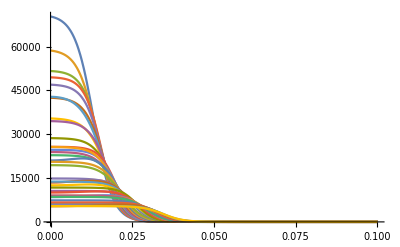

```mathematica
(* All rho plots *)
rho$mean = Transpose[Transpose[Total$List$N10$muLBis01C][[1]]][[1]];
Plot[rho$mean,{r,0,0.1},PlotRange->All]
```

```mathematica
(* RMS table *)
(* Units of fm (for comparison) *)
r$rms=Transpose@{Z$List,Transpose[Total$List$N10$muLBis01C][[2]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[r$rms,{"Z",ToString[Subscript["r","rms"],StandardForm]<>" (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | r_rms (fm)
9 | 2.9160.033
10 | 3.0370.019
12 | 3.050.08
13 | 3.050.06
14 | 3.140.06
15 | 3.2427
16 | 3.2410.023
18 | 3.4690.020
20 | 3.410.05
22 | 3.5790.025
23 | 3.5820.030
24 | 3.6600.017
25 | 3.6800.009
26 | 3.7880.013
27 | 3.800.05
28 | 3.7580.005
29 | 3.920.04
30 | 4.0430.013
38 | 4.2610.013
39 | 4.270.08
40 | 4.2740.009
41 | 4.360.06
42 | 4.4300.010
48 | 4.6310.018
49 | 4.460.13
50 | 4.6450.011
56 | 4.83707
57 | 4.870.07
60 | 4.9160.007
62 | 4.9850.023
67 | 5.19249
73 | 5.48473
74 | 5.460.11
79 | 5.320.09
82 | 5.520.04
83 | 5.5190.021
90 | 5.6770.032
92 | 5.7330.023

```mathematica
(* c, z, and w param tables *)
rho$params=Transpose@{Z$List,Transpose[Total$List$N10$muLBis01C][[3]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N10$muLBis01C][[4]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N10$muLBis01C][[5]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[rho$params,{"Z","c (fm)","z (fm)","w (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | c (fm) | z (fm) | w (fm)
9 | 2.600.04 | 0.5670.014 | 0
10 | 2.8020.020 | 0.5720.006 | 0
12 | 3.0030.027 | 0.5300.031 | 0
13 | 3.080.08 | 0.5100.026 | 0
14 | 3.110.04 | 0.5410.021 | 0
15 | 3.21 | 0.56 | 0
16 | 2.550.09 | 2.1910.011 | 0.1590.009
18 | 3.3960.013 | 0.6080.008 | 0
20 | 3.480.08 | 0.563 | 0
22 | 3.730.04 | 0.567 | 0
23 | 3.9480.026 | 0.5020.013 | 0
24 | 3.9840.022 | 0.5290.006 | 0
25 | 3.8950.014 | 0.567 | 0
26 | 3.9740.014 | 0.5940.004 | 0
27 | 4.070.08 | 0.569 | 0
28 | 3.6040.008 | 2.31120.0023 | 0.4080.010
29 | 4.2170.024 | 0.5820.019 | 0
30 | 4.2700.012 | 0.62540.0031 | 0
38 | 4.2530.012 | 2.5470.007 | 0.4640.028
39 | 4.760.05 | 0.580.04 | 0
40 | 4.4360.018 | 2.5280.004 | 0.3490.018
41 | 4.890.04 | 0.5820.030 | 0
42 | 4.5610.017 | 2.64900.0031 | 0.3160.019
48 | 5.4060.023 | 0.5320.008 | 0
49 | 5.240.10 | 0.500.06 | 0
50 | 5.1120.009 | 2.61810.0032 | 0.2900.021
56 | 5.3376 | 2.6776 | 0.3749
57 | 5.740.06 | 0.5370.028 | 0
60 | 5.6838 | 0.5880.004 | 0
62 | 5.8044 | 0.5790.014 | 0
67 | 6.12 | 0.57 | 0
73 | 6.38 | 0.64 | 0
74 | 6.530.09 | 0.550.05 | 0
79 | 6.360.09 | 0.5380.033 | 0
82 | 6.630.05 | 0.5470.007 | 0
83 | 6.3140.011 | 2.8810.006 | 0.390.06
90 | 6.7915 | 0.5730.024 | 0
92 | 6.8054 | 0.6060.016 | 0

### E-field and potential plots with no SD

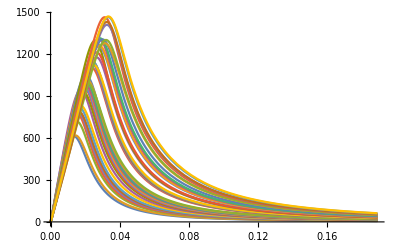

```mathematica
(* All E-field plots *)
Ef$mean = Transpose[Transpose[Total$List$N10$muLBis01C][[6]]][[1]];
Plot[Ef$mean,{r,0,0.2 inf},PlotRange->All]
```

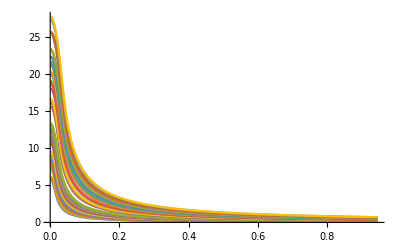

```mathematica
(* All potential plots *)
V$mean = Transpose[Transpose[Total$List$N10$muLBis01C][[7]]][[1]];
Plot[V$mean,{r,eps,inf},PlotRange->All]
```

### e.w.f. and m.w.f plots

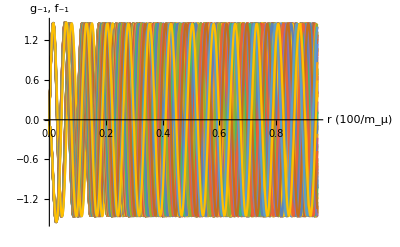

```mathematica
(* All e.w.f. plots *)
u1$e$List=Transpose[Transpose[Total$List$N10$muLBis01C][[15]]][[1]];
u2$e$List=Transpose[Transpose[Total$List$N10$muLBis01C][[16]]][[1]];
u1$e$Plot=Plot[u1$e$List,{r,0,inf},PlotRange->All];
u2$e$Plot=Plot[u2$e$List,{r,0,inf},PlotRange->All];
Show[u1$e$Plot,u2$e$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Subscript["g",-1],StandardForm] <>", "<>ToString[Subscript["f",-1],StandardForm] }]
```

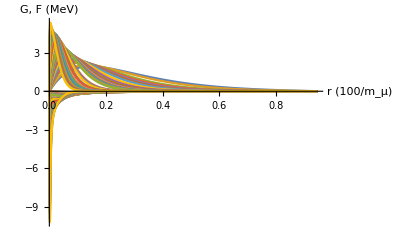

```mathematica
(* All m.w.f. plots *)
u1$mu$List=Transpose[Transpose[Total$List$N10$muLBis01C][[17]]][[1]];
u2$mu$List=Transpose[Transpose[Total$List$N10$muLBis01C][[18]]][[1]];
u1$mu$Plot=Plot[u1$mu$List,{r,0,inf},PlotRange->All];
u2$mu$Plot=Plot[u2$mu$List,{r,0,inf},PlotRange->All];
Show[u1$mu$Plot,u2$mu$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F "<>ToString[Superscript["(MeV)","(1/2)"],StandardForm] }]
```

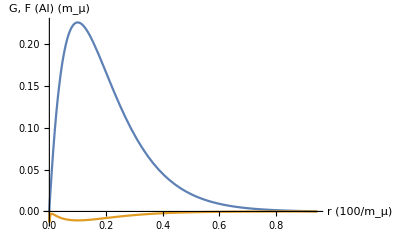

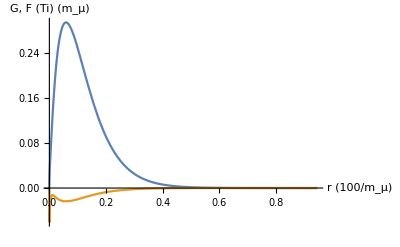

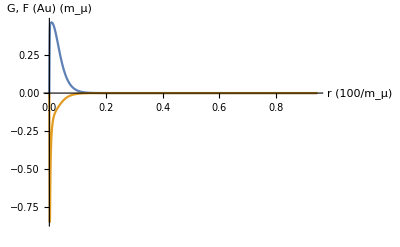

```mathematica
(* Some m.w.f. plots with uncertainty *)
Plot[{u1$mu$List[[4]]/Sqrt[mmu],u2$mu$List[[4]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Al)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[10]]/Sqrt[mmu],u2$mu$List[[10]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Ti)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[34]]/Sqrt[mmu],u2$mu$List[[34]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Au)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
```

### FA plots (with and without SD) and tables with SD

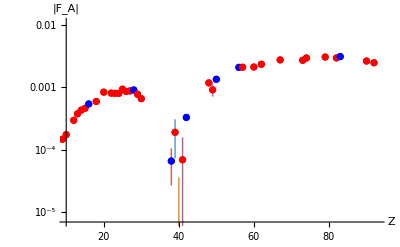

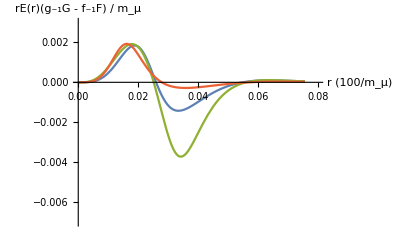

Z | F_A×10
9 | 1.480.05
10 | 1.760.04
12 | 2.980.24
13 | 3.780.26
14 | 4.330.32
15 | 4.6415
16 | 5.440.21
18 | 5.960.14
20 | 8.40.7
22 | 8.10.4
23 | 8.10.4
24 | 8.050.28
25 | 9.380.20
26 | 8.620.23
27 | 8.81.2
28 | 9.120.16
29 | 7.80.5
30 | 6.620.24
38 | 0.70.4
39 | 1.91.2
40 | -0.040.32
41 | -0.70.9
42 | -3.310.34
48 | -11.840.33
49 | -9.22.0
50 | -13.50.4
56 | -20.9742
57 | -21.10.5
60 | -21.270.07
62 | -23.540.30
67 | -27.6344
73 | -27.2452
74 | -29.71.7
79 | -30.71.1
82 | -29.720.34
83 | -31.210.32
90 | -26.50.7
92 | -24.90.5

```mathematica
(* FA plots and tables with uncertainty *)
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
FA$Integrand$mean=Transpose[Transpose[Total$List$N10$muLBis01C][[8]]][[1]];
FA$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis01C][[9]]/.{x_,y_}->Around[x,y]};
ListLogPlot[{#}&/@Abs[FA$List],PlotStyle->PlotColors,PlotRange->{{10,93},{0.000007,0.011}}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","A"],StandardForm] <> "|" }]

Plot[{FA$Integrand$mean[[19]]/mmu,,FA$Integrand$mean[[34]]/mmu,5FA$Integrand$mean[[4]]/mmu},{r,0,0.08 inf},PlotRange->{{0,0.08},{-0.007,0.003}}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm] <> ToString[Superscript["E",2],StandardForm]<>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[FA$List/.{x_,y_}->{x,y*10^4},{"Z",ToString[Cross[Subscript["F","A"],Superscript["10","4"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

### other O.I. plots and tables with SD

```mathematica
(* D and other O.I. plots and tables with uncertainty *)
D$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis01C][[10]]/.{x_,y_}->Around[x,y]};
Sp$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis01C][[11]]/.{x_,y_}->Around[x,y]};
Vp$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis01C][[12]]/.{x_,y_}->Around[x,y]};
Sn$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis01C][[13]]/.{x_,y_}->Around[x,y]};
Vn$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis01C][[14]]/.{x_,y_}->Around[x,y]};

D$Plot=ListLinePlot[D$List,PlotMarkers->"+",PlotStyle->Black,PlotRange->All];
Sp$Plot=ListLinePlot[Sp$List,PlotMarkers->"x",PlotStyle->{Red,Dashed},PlotRange->All];
Vp$Plot=ListLinePlot[Vp$List,PlotMarkers->"✶",PlotStyle->{Blue,Dotted},PlotRange->All];
Sn$Plot=ListLinePlot[Sn$List,PlotMarkers->"□",PlotStyle->{Magenta,Dashed},PlotRange->All];
Vn$Plot=ListLinePlot[Vn$List,PlotMarkers->"■",PlotStyle->{Green,Dotted},PlotRange->All];
Show[D$Plot,Sp$Plot,Vp$Plot,Sn$Plot,Vn$Plot,PlotRange->{{0,100},All},AxesLabel->{"Z" , "Overlap Integrals ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}]

DSpVp$data={};
For[i=1,i≤Length[D$List],i++,
AppendTo[DSpVp$data,{D$List[[i]][[1]],D$List[[i]][[2]],D$List[[i]][[2]]/(8e),Sp$List[[i]][[2]],Vp$List[[i]][[2]],Sn$List[[i]][[2]],Vn$List[[i]][[2]]}]
]

Text@Grid[Prepend[DSpVp$data,{"Z","D ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")","D/(8e)~Vp~Sp",ToString[Subscript["S","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["S","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,12,12,12,12,12,12}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

Z | D (m_μ) | D/(8e)~Vp~Sp | S_p (m_μ) | V_p (m_μ) | S_n (m_μ) | V_n (m_μ)
9 | 0.017400.00016 | 0.007180.00007 | 0.007420.00007 | 0.007720.00007 | 0.008250.00008 | 0.008580.00008
10 | 0.021440.00013 | 0.008850.00005 | 0.009140.00006 | 0.009600.00006 | 0.009140.00006 | 0.009600.00006
12 | 0.03280.0008 | 0.013530.00032 | 0.01400.0004 | 0.014930.00034 | 0.01400.0004 | 0.014930.00034
13 | 0.03950.0007 | 0.016320.00031 | 0.016910.00034 | 0.018150.00034 | 0.01820.0004 | 0.01950.0004
14 | 0.04570.0009 | 0.01880.0004 | 0.01950.0004 | 0.02120.0004 | 0.01950.0004 | 0.02120.0004
15 | 0.0515686 | 0.0212867 | 0.0219823 | 0.02411 | 0.0234478 | 0.0257173
16 | 0.05940.0006 | 0.024520.00024 | 0.025280.00027 | 0.028010.00027 | 0.025280.00027 | 0.028010.00027
18 | 0.07200.0005 | 0.029710.00021 | 0.030500.00023 | 0.034520.00023 | 0.037280.00028 | 0.042190.00028
20 | 0.09240.0020 | 0.03810.0008 | 0.03920.0010 | 0.04490.0010 | 0.03920.0010 | 0.04490.0010
22 | 0.10590.0013 | 0.04370.0005 | 0.04460.0006 | 0.05220.0006 | 0.05270.0007 | 0.06170.0008
23 | 0.11440.0014 | 0.04720.0006 | 0.04800.0006 | 0.05670.0007 | 0.05840.0008 | 0.06900.0008
24 | 0.12170.0009 | 0.05020.0004 | 0.05080.0004 | 0.06070.0005 | 0.05930.0005 | 0.07090.0005
25 | 0.13310.0006 | 0.054950.00025 | 0.055580.00029 | 0.067050.00030 | 0.066690.00035 | 0.08050.0004
26 | 0.13830.0008 | 0.057080.00034 | 0.05730.0004 | 0.07030.0004 | 0.06620.0004 | 0.08110.0005
27 | 0.1480.004 | 0.06110.0016 | 0.06120.0018 | 0.07560.0020 | 0.07250.0022 | 0.08960.0023
28 | 0.15950.0005 | 0.065830.00021 | 0.065710.00024 | 0.081890.00026 | 0.070400.00025 | 0.087740.00028
29 | 0.16190.0024 | 0.06680.0010 | 0.06620.0011 | 0.08400.0012 | 0.07760.0013 | 0.09850.0014
30 | 0.16500.0010 | 0.06810.0004 | 0.06690.0005 | 0.08640.0005 | 0.07580.0006 | 0.09800.0006
38 | 0.22480.0019 | 0.09280.0008 | 0.08670.0009 | 0.12390.0010 | 0.11410.0011 | 0.16310.0013
39 | 0.2400.007 | 0.09910.0031 | 0.09280.0034 | 0.1330.004 | 0.1190.004 | 0.1710.005
40 | 0.24520.0015 | 0.10120.0006 | 0.09380.0007 | 0.13690.0008 | 0.11720.0009 | 0.17120.0010
41 | 0.2500.007 | 0.10330.0028 | 0.09520.0030 | 0.14090.0035 | 0.1210.004 | 0.1790.004
42 | 0.24790.0018 | 0.10230.0007 | 0.09280.0008 | 0.14080.0010 | 0.12380.0011 | 0.18780.0013
48 | 0.27390.0029 | 0.11310.0012 | 0.09730.0013 | 0.16160.0016 | 0.13370.0018 | 0.22220.0022
49 | 0.3130.019 | 0.1290.008 | 0.1130.008 | 0.1850.010 | 0.1530.011 | 0.2490.014
50 | 0.28920.0025 | 0.11940.0010 | 0.10150.0011 | 0.17250.0015 | 0.14210.0016 | 0.24150.0021
56 | 0.305641 | 0.126164 | 0.101246 | 0.188968 | 0.148254 | 0.276703
57 | 0.3120.012 | 0.1290.005 | 0.1030.005 | 0.1950.007 | 0.1490.007 | 0.2800.010
60 | 0.33820.0007 | 0.139590.00030 | 0.111190.00027 | 0.21390.0004 | 0.15200.0004 | 0.29240.0006
62 | 0.33720.0025 | 0.13920.0010 | 0.10850.0009 | 0.21580.0014 | 0.15750.0013 | 0.31320.0020
67 | 0.326664 | 0.134842 | 0.0994141 | 0.214729 | 0.145412 | 0.314081
73 | 0.314007 | 0.129617 | 0.0909119 | 0.212741 | 0.1345 | 0.31474
74 | 0.3090.017 | 0.1280.007 | 0.0880.006 | 0.2100.011 | 0.1300.009 | 0.3120.016
79 | 0.3640.018 | 0.1500.007 | 0.1050.006 | 0.2500.012 | 0.1560.010 | 0.3730.017
82 | 0.3350.008 | 0.13830.0032 | 0.09290.0027 | 0.2330.005 | 0.1430.004 | 0.3580.008
83 | 0.3260.007 | 0.13470.0030 | 0.08820.0028 | 0.2270.005 | 0.1340.004 | 0.3450.008
90 | 0.33770.0028 | 0.13940.0012 | 0.09150.0007 | 0.23970.0019 | 0.14430.0011 | 0.37810.0029
92 | 0.33840.0020 | 0.13970.0008 | 0.09160.0005 | 0.24120.0013 | 0.14540.0008 | 0.38280.0021

## Nreps = 10, muon lower bound is 0.5c

### Rho plots no SD, RMS table with SD, rho params table with SD

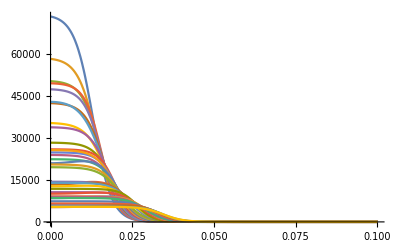

```mathematica
(* All rho plots *)
rho$mean = Transpose[Transpose[Total$List$N10$muLBis05C][[1]]][[1]];
Plot[rho$mean,{r,0,0.1},PlotRange->All]
```

```mathematica
(* RMS table *)
(* Units of fm (for comparison) *)
r$rms=Transpose@{Z$List,Transpose[Total$List$N10$muLBis05C][[2]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[r$rms,{"Z",ToString[Subscript["r","rms"],StandardForm]<>" (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | r_rms (fm)
9 | 2.870.05
10 | 3.0430.012
12 | 3.100.08
13 | 3.040.10
14 | 3.120.04
15 | 3.2427
16 | 3.2360.013
18 | 3.4880.032
20 | 3.430.04
22 | 3.5890.022
23 | 3.570.05
24 | 3.6540.027
25 | 3.6780.007
26 | 3.7880.012
27 | 3.810.04
28 | 3.7590.008
29 | 3.930.04
30 | 4.0360.013
38 | 4.2630.014
39 | 4.300.05
40 | 4.2800.015
41 | 4.350.05
42 | 4.4220.015
48 | 4.6280.014
49 | 4.450.12
50 | 4.6420.006
56 | 4.83707
57 | 4.840.10
60 | 4.9130.006
62 | 4.9870.027
67 | 5.19249
73 | 5.48473
74 | 5.430.07
79 | 5.350.06
82 | 5.5290.028
83 | 5.5270.031
90 | 5.6750.017
92 | 5.7360.019

```mathematica
(* c, z, and w param tables *)
rho$params=Transpose@{Z$List,Transpose[Total$List$N10$muLBis05C][[3]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N10$muLBis05C][[4]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N10$muLBis05C][[5]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[rho$params,{"Z","c (fm)","z (fm)","w (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | c (fm) | z (fm) | w (fm)
9 | 2.560.05 | 0.5580.015 | 0
10 | 2.8070.016 | 0.5730.005 | 0
12 | 3.0100.035 | 0.5510.030 | 0
13 | 3.080.08 | 0.5070.035 | 0
14 | 3.0990.034 | 0.5360.013 | 0
15 | 3.21 | 0.56 | 0
16 | 2.540.09 | 2.1870.007 | 0.1620.019
18 | 3.3870.013 | 0.6180.013 | 0
20 | 3.510.06 | 0.563 | 0
22 | 3.7500.035 | 0.567 | 0
23 | 3.9330.028 | 0.5030.020 | 0
24 | 3.9730.034 | 0.5300.013 | 0
25 | 3.8920.010 | 0.567 | 0
26 | 3.9700.014 | 0.59500.0032 | 0
27 | 4.100.06 | 0.569 | 0
28 | 3.5960.017 | 2.31120.0029 | 0.4160.014
29 | 4.2110.029 | 0.5910.019 | 0
30 | 4.2580.014 | 0.62570.0025 | 0
38 | 4.2540.011 | 2.5480.008 | 0.470.04
39 | 4.820.04 | 0.5730.032 | 0
40 | 4.4370.018 | 2.5290.004 | 0.3610.028
41 | 4.860.04 | 0.5860.035 | 0
42 | 4.5630.018 | 2.6510.004 | 0.2910.021
48 | 5.4000.016 | 0.5330.008 | 0
49 | 5.220.12 | 0.490.06 | 0
50 | 5.1040.007 | 2.61970.0027 | 0.2880.010
56 | 5.3376 | 2.6776 | 0.3749
57 | 5.710.09 | 0.5270.032 | 0
60 | 5.6838 | 0.5870.004 | 0
62 | 5.8044 | 0.5800.017 | 0
67 | 6.12 | 0.57 | 0
73 | 6.38 | 0.64 | 0
74 | 6.520.07 | 0.5370.034 | 0
79 | 6.390.07 | 0.5460.024 | 0
82 | 6.6410.035 | 0.5460.004 | 0
83 | 6.3150.011 | 2.8790.009 | 0.410.10
90 | 6.7915 | 0.5720.012 | 0
92 | 6.8054 | 0.6080.013 | 0

### E-field and potential plots with no SD

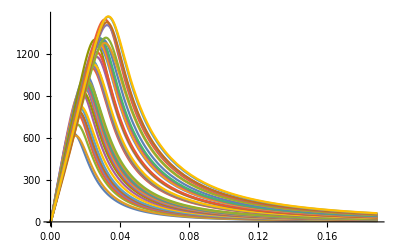

```mathematica
(* All E-field plots *)
Ef$mean = Transpose[Transpose[Total$List$N10$muLBis05C][[6]]][[1]];
Plot[Ef$mean,{r,0,0.2 inf},PlotRange->All]
```

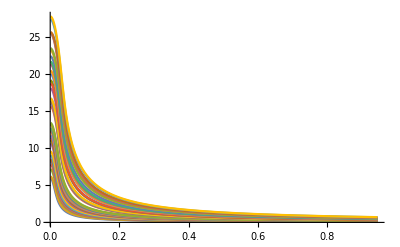

```mathematica
(* All potential plots *)
V$mean = Transpose[Transpose[Total$List$N10$muLBis05C][[7]]][[1]];
Plot[V$mean,{r,eps,inf},PlotRange->All]
```

### e.w.f. and m.w.f plots

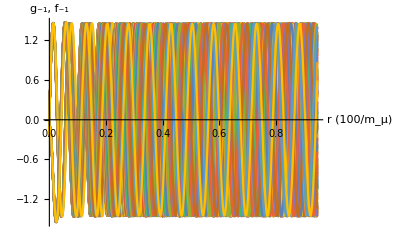

```mathematica
(* All e.w.f. plots *)
u1$e$List=Transpose[Transpose[Total$List$N10$muLBis05C][[15]]][[1]];
u2$e$List=Transpose[Transpose[Total$List$N10$muLBis05C][[16]]][[1]];
u1$e$Plot=Plot[u1$e$List,{r,0,inf},PlotRange->All];
u2$e$Plot=Plot[u2$e$List,{r,0,inf},PlotRange->All];
Show[u1$e$Plot,u2$e$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Subscript["g",-1],StandardForm] <>", "<>ToString[Subscript["f",-1],StandardForm] }]
```

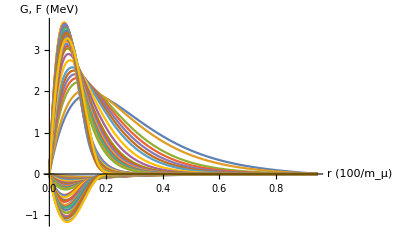

```mathematica
(* All m.w.f. plots *)
u1$mu$List=Transpose[Transpose[Total$List$N10$muLBis05C][[17]]][[1]];
u2$mu$List=Transpose[Transpose[Total$List$N10$muLBis05C][[18]]][[1]];
u1$mu$Plot=Plot[u1$mu$List,{r,0,inf},PlotRange->All];
u2$mu$Plot=Plot[u2$mu$List,{r,0,inf},PlotRange->All];
Show[u1$mu$Plot,u2$mu$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F "<>ToString[Superscript["(MeV)","(1/2)"],StandardForm] }]
```

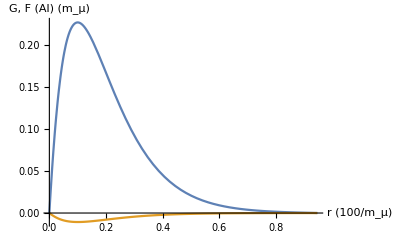

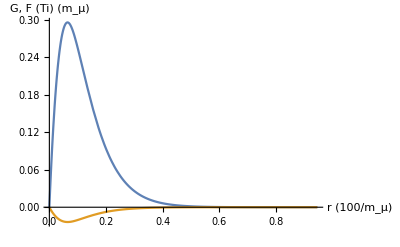

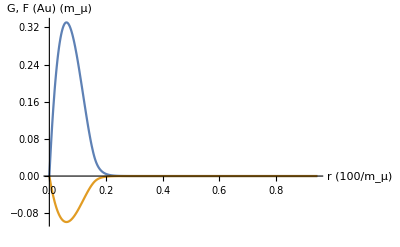

```mathematica
(* Some m.w.f. plots with uncertainty *)
Plot[{u1$mu$List[[4]]/Sqrt[mmu],u2$mu$List[[4]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Al)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[10]]/Sqrt[mmu],u2$mu$List[[10]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Ti)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[34]]/Sqrt[mmu],u2$mu$List[[34]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Au)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
```

### FA plots (with and without SD) and tables with SD

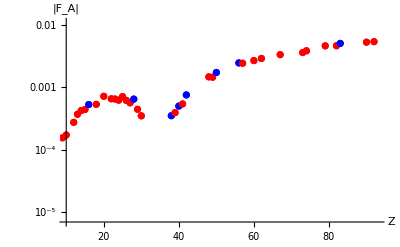

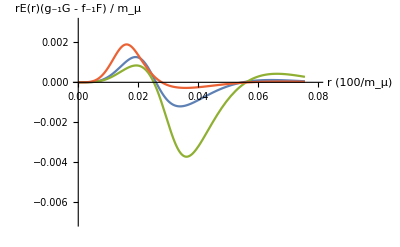

Z | F_A×10
9 | 1.560.09
10 | 1.7330.024
12 | 2.760.23
13 | 3.70.5
14 | 4.270.25
15 | 4.43287
16 | 5.330.14
18 | 5.360.20
20 | 7.20.5
22 | 6.580.32
23 | 6.50.5
24 | 6.260.34
25 | 7.150.12
26 | 6.210.18
27 | 5.70.7
28 | 6.510.17
29 | 4.50.4
30 | 3.510.18
38 | -3.530.30
39 | -3.950.35
40 | -5.030.32
41 | -5.50.4
42 | -7.590.30
48 | -14.780.12
49 | -14.61.3
50 | -17.380.07
56 | -24.7295
57 | -24.40.4
60 | -26.960.07
62 | -29.120.32
67 | -33.5175
73 | -36.2523
74 | -38.71.1
79 | -46.41.0
82 | -46.60.4
83 | -50.780.13
90 | -53.10.5
92 | -54.10.5

```mathematica
(* FA plots and tables with uncertainty *)
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
FA$Integrand$mean=Transpose[Transpose[Total$List$N10$muLBis05C][[8]]][[1]];
FA$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis05C][[9]]/.{x_,y_}->Around[x,y]};
ListLogPlot[{#}&/@Abs[FA$List],PlotStyle->PlotColors,PlotRange->{{10,93},{0.000007,0.011}}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","A"],StandardForm] <> "|" }]

Plot[{FA$Integrand$mean[[19]]/mmu,,FA$Integrand$mean[[34]]/mmu,5FA$Integrand$mean[[4]]/mmu},{r,0,0.08 inf},PlotRange->{{0,0.08},{-0.007,0.003}}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm] <> ToString[Superscript["E",2],StandardForm]<>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[FA$List/.{x_,y_}->{x,y*10^4},{"Z",ToString[Cross[Subscript["F","A"],Superscript["10","4"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

### other O.I. plots and tables with SD

```mathematica
(* D and other O.I. plots and tables with uncertainty *)
D$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis05C][[10]]/.{x_,y_}->Around[x,y]};
Sp$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis05C][[11]]/.{x_,y_}->Around[x,y]};
Vp$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis05C][[12]]/.{x_,y_}->Around[x,y]};
Sn$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis05C][[13]]/.{x_,y_}->Around[x,y]};
Vn$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis05C][[14]]/.{x_,y_}->Around[x,y]};

D$Plot=ListLinePlot[D$List,PlotMarkers->"+",PlotStyle->Black,PlotRange->All];
Sp$Plot=ListLinePlot[Sp$List,PlotMarkers->"x",PlotStyle->{Red,Dashed},PlotRange->All];
Vp$Plot=ListLinePlot[Vp$List,PlotMarkers->"✶",PlotStyle->{Blue,Dotted},PlotRange->All];
Sn$Plot=ListLinePlot[Sn$List,PlotMarkers->"□",PlotStyle->{Magenta,Dashed},PlotRange->All];
Vn$Plot=ListLinePlot[Vn$List,PlotMarkers->"■",PlotStyle->{Green,Dotted},PlotRange->All];
Show[D$Plot,Sp$Plot,Vp$Plot,Sn$Plot,Vn$Plot,PlotRange->{{0,100},All},AxesLabel->{"Z" , "Overlap Integrals ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}]

DSpVp$data={};
For[i=1,i≤Length[D$List],i++,
AppendTo[DSpVp$data,{D$List[[i]][[1]],D$List[[i]][[2]],D$List[[i]][[2]]/(8e),Sp$List[[i]][[2]],Vp$List[[i]][[2]],Sn$List[[i]][[2]],Vn$List[[i]][[2]]}]
]

Text@Grid[Prepend[DSpVp$data,{"Z","D ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")","D/(8e)~Vp~Sp",ToString[Subscript["S","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["S","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,12,12,12,12,12,12}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

Z | D (m_μ) | D/(8e)~Vp~Sp | S_p (m_μ) | V_p (m_μ) | S_n (m_μ) | V_n (m_μ)
9 | 0.017690.00028 | 0.007300.00011 | 0.007560.00012 | 0.007830.00012 | 0.008400.00014 | 0.008700.00014
10 | 0.021340.00008 | 0.0088110.000034 | 0.009100.00004 | 0.009500.00004 | 0.009100.00004 | 0.009500.00004
12 | 0.03170.0008 | 0.013100.00033 | 0.01350.0004 | 0.01430.0004 | 0.01350.0004 | 0.01430.0004
13 | 0.03870.0013 | 0.01600.0005 | 0.01650.0006 | 0.01750.0006 | 0.01780.0006 | 0.01890.0006
14 | 0.04460.0007 | 0.018400.00029 | 0.019010.00032 | 0.020280.00032 | 0.019010.00032 | 0.020280.00032
15 | 0.0495211 | 0.0204415 | 0.021052 | 0.0226364 | 0.0224555 | 0.0241455
16 | 0.058090.00034 | 0.023980.00014 | 0.024740.00016 | 0.026740.00016 | 0.024740.00016 | 0.026740.00016
18 | 0.06630.0008 | 0.027360.00031 | 0.027930.00034 | 0.030740.00035 | 0.03410.0004 | 0.03760.0004
20 | 0.08270.0014 | 0.03410.0006 | 0.03480.0006 | 0.03870.0006 | 0.03480.0006 | 0.03870.0006
22 | 0.09080.0010 | 0.03750.0004 | 0.03780.0004 | 0.04290.0005 | 0.04460.0005 | 0.05070.0005
23 | 0.09610.0020 | 0.03970.0008 | 0.03980.0009 | 0.04560.0009 | 0.04850.0011 | 0.05550.0011
24 | 0.10010.0012 | 0.04130.0005 | 0.04130.0005 | 0.04780.0006 | 0.04810.0006 | 0.05570.0006
25 | 0.10850.0004 | 0.044790.00015 | 0.044670.00016 | 0.052000.00017 | 0.053610.00020 | 0.062400.00020
26 | 0.10980.0006 | 0.045320.00027 | 0.044890.00029 | 0.052910.00030 | 0.051800.00033 | 0.061050.00035
27 | 0.11320.0023 | 0.04670.0010 | 0.04600.0010 | 0.05480.0011 | 0.05450.0012 | 0.06500.0013
28 | 0.12930.0006 | 0.053360.00023 | 0.052520.00025 | 0.062980.00026 | 0.056270.00027 | 0.067480.00028
29 | 0.11800.0019 | 0.04870.0008 | 0.04750.0008 | 0.05780.0009 | 0.05560.0010 | 0.06780.0010
30 | 0.11830.0008 | 0.048810.00032 | 0.047200.00034 | 0.05830.0004 | 0.05350.0004 | 0.06610.0004
38 | 0.14190.0014 | 0.05860.0006 | 0.05380.0006 | 0.07370.0006 | 0.07070.0008 | 0.09700.0009
39 | 0.13310.0030 | 0.05500.0012 | 0.05030.0012 | 0.06980.0014 | 0.06450.0016 | 0.08950.0019
40 | 0.14520.0016 | 0.05990.0007 | 0.05440.0007 | 0.07640.0007 | 0.06800.0009 | 0.09550.0009
41 | 0.13560.0031 | 0.05600.0013 | 0.05060.0013 | 0.07200.0016 | 0.06420.0017 | 0.09140.0020
42 | 0.13970.0016 | 0.05770.0007 | 0.05140.0007 | 0.07490.0007 | 0.06850.0009 | 0.09990.0010
48 | 0.11840.0010 | 0.04890.0004 | 0.04140.0004 | 0.06820.0005 | 0.05690.0005 | 0.09380.0007
49 | 0.1410.010 | 0.0580.004 | 0.0500.004 | 0.0800.005 | 0.0670.006 | 0.1080.007
50 | 0.12940.0006 | 0.053420.00026 | 0.044440.00026 | 0.075260.00030 | 0.06220.0004 | 0.10540.0004
56 | 0.119402 | 0.0492871 | 0.0382777 | 0.0747934 | 0.0560495 | 0.109519
57 | 0.1130.008 | 0.04680.0033 | 0.03640.0031 | 0.0720.004 | 0.0520.004 | 0.1040.006
60 | 0.117350.00034 | 0.048440.00014 | 0.036690.00013 | 0.076030.00019 | 0.050140.00017 | 0.103910.00027
62 | 0.11060.0014 | 0.04570.0006 | 0.03350.0005 | 0.07410.0008 | 0.04870.0007 | 0.10760.0012
67 | 0.0918782 | 0.0379258 | 0.0252038 | 0.0682134 | 0.0368652 | 0.0997749
73 | 0.0749307 | 0.0309302 | 0.0175478 | 0.0631594 | 0.0259612 | 0.0934412
74 | 0.0710.005 | 0.02940.0020 | 0.01600.0017 | 0.06260.0027 | 0.02380.0025 | 0.0930.004
79 | 0.0890.005 | 0.03660.0022 | 0.01980.0018 | 0.07610.0029 | 0.02960.0027 | 0.1140.004
82 | 0.07200.0024 | 0.02970.0010 | 0.01360.0008 | 0.06920.0013 | 0.02090.0012 | 0.10640.0019
83 | 0.0760.004 | 0.03130.0018 | 0.01360.0015 | 0.07370.0020 | 0.02060.0022 | 0.11190.0030
90 | 0.07040.0006 | 0.029070.00023 | 0.010470.00015 | 0.07410.0004 | 0.016520.00024 | 0.11690.0007
92 | 0.07110.0006 | 0.029330.00026 | 0.009980.00017 | 0.07560.0005 | 0.015830.00027 | 0.11990.0008

## Nreps = 10, muon lower bound is c

### Rho plots no SD, RMS table with SD, rho params table with SD

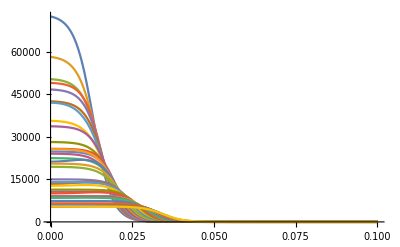

```mathematica
(* All rho plots *)
rho$mean = Transpose[Transpose[Total$List$N10$muLBisC][[1]]][[1]];
Plot[rho$mean,{r,0,0.1},PlotRange->All]
```

```mathematica
(* RMS table *)
(* Units of fm (for comparison) *)
r$rms=Transpose@{Z$List,Transpose[Total$List$N10$muLBisC][[2]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[r$rms,{"Z",ToString[Subscript["r","rms"],StandardForm]<>" (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | r_rms (fm)
9 | 2.890.04
10 | 3.0440.016
12 | 3.110.08
13 | 3.080.09
14 | 3.150.05
15 | 3.2427
16 | 3.2520.023
18 | 3.4730.017
20 | 3.4330.029
22 | 3.5950.021
23 | 3.5840.030
24 | 3.660.04
25 | 3.6800.007
26 | 3.7810.011
27 | 3.8110.023
28 | 3.7530.009
29 | 3.9070.035
30 | 4.0440.014
38 | 4.2620.013
39 | 4.240.06
40 | 4.2790.010
41 | 4.320.04
42 | 4.4180.010
48 | 4.6310.023
49 | 4.520.12
50 | 4.6440.005
56 | 4.83707
57 | 4.850.06
60 | 4.91370.0031
62 | 4.9860.014
67 | 5.19249
73 | 5.48473
74 | 5.430.07
79 | 5.350.04
82 | 5.5200.025
83 | 5.5200.018
90 | 5.6780.015
92 | 5.7260.020

```mathematica
(* c, z, and w param tables *)
rho$params=Transpose@{Z$List,Transpose[Total$List$N10$muLBisC][[3]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N10$muLBisC][[4]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N10$muLBisC][[5]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[rho$params,{"Z","c (fm)","z (fm)","w (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | c (fm) | z (fm) | w (fm)
9 | 2.5750.027 | 0.5620.014 | 0
10 | 2.8110.020 | 0.57250.0033 | 0
12 | 3.010.05 | 0.5530.031 | 0
13 | 3.080.08 | 0.5240.020 | 0
14 | 3.110.04 | 0.5460.016 | 0
15 | 3.21 | 0.56 | 0
16 | 2.600.08 | 2.1930.009 | 0.1620.015
18 | 3.3820.011 | 0.6130.008 | 0
20 | 3.510.05 | 0.563 | 0
22 | 3.7600.034 | 0.567 | 0
23 | 3.9430.032 | 0.5040.014 | 0
24 | 3.9770.019 | 0.5300.015 | 0
25 | 3.8950.012 | 0.567 | 0
26 | 3.9670.007 | 0.5930.004 | 0
27 | 4.090.04 | 0.569 | 0
28 | 3.5990.010 | 2.31090.0034 | 0.3980.016
29 | 4.2280.029 | 0.5730.018 | 0
30 | 4.2700.019 | 0.6260.004 | 0
38 | 4.2560.011 | 2.5450.007 | 0.4730.035
39 | 4.750.04 | 0.5670.027 | 0
40 | 4.4380.014 | 2.52890.0033 | 0.3560.021
41 | 4.870.05 | 0.5680.021 | 0
42 | 4.5530.015 | 2.64870.0029 | 0.2960.018
48 | 5.3950.018 | 0.5370.010 | 0
49 | 5.290.11 | 0.520.06 | 0
50 | 5.1100.007 | 2.61690.0022 | 0.2910.014
56 | 5.3376 | 2.6776 | 0.3749
57 | 5.730.06 | 0.5290.019 | 0
60 | 5.6838 | 0.58700.0019 | 0
62 | 5.8044 | 0.5800.009 | 0
67 | 6.12 | 0.57 | 0
73 | 6.38 | 0.64 | 0
74 | 6.520.07 | 0.530.04 | 0
79 | 6.410.06 | 0.5380.021 | 0
82 | 6.6230.026 | 0.5480.009 | 0
83 | 6.3110.008 | 2.8800.009 | 0.390.05
90 | 6.7915 | 0.5750.011 | 0
92 | 6.8054 | 0.6020.014 | 0

### E-field and potential plots with no SD

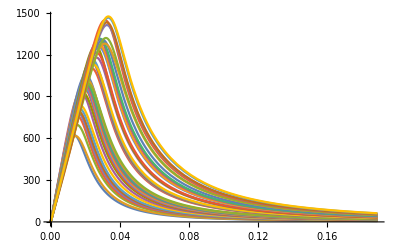

```mathematica
(* All E-field plots *)
Ef$mean = Transpose[Transpose[Total$List$N10$muLBisC][[6]]][[1]];
Plot[Ef$mean,{r,0,0.2 inf},PlotRange->All]
```

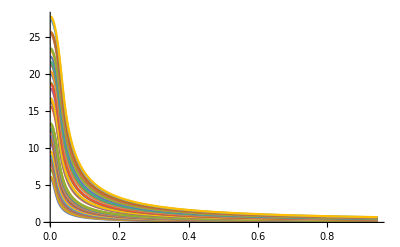

```mathematica
(* All potential plots *)
V$mean = Transpose[Transpose[Total$List$N10$muLBisC][[7]]][[1]];
Plot[V$mean,{r,eps,inf},PlotRange->All]
```

### e.w.f. and m.w.f plots

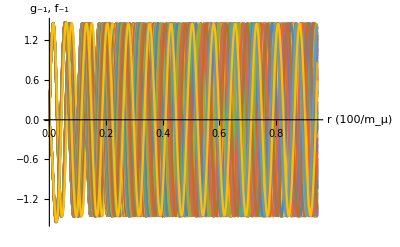

```mathematica
(* All e.w.f. plots *)
u1$e$List=Transpose[Transpose[Total$List$N10$muLBisC][[15]]][[1]];
u2$e$List=Transpose[Transpose[Total$List$N10$muLBisC][[16]]][[1]];
u1$e$Plot=Plot[u1$e$List,{r,0,inf},PlotRange->All];
u2$e$Plot=Plot[u2$e$List,{r,0,inf},PlotRange->All];
Show[u1$e$Plot,u2$e$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Subscript["g",-1],StandardForm] <>", "<>ToString[Subscript["f",-1],StandardForm] }]
```

```mathematica
(* All m.w.f. plots *)
u1$mu$List=Transpose[Transpose[Total$List$N10$muLBisC][[17]]][[1]];
u2$mu$List=Transpose[Transpose[Total$List$N10$muLBisC][[18]]][[1]];
u1$mu$Plot=Plot[u1$mu$List,{r,0,inf},PlotRange->All];
u2$mu$Plot=Plot[u2$mu$List,{r,0,inf},PlotRange->All];
Show[u1$mu$Plot,u2$mu$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F "<>ToString[Superscript["(MeV)","(1/2)"],StandardForm] }]
```

-Graphics-

```mathematica
(* Some m.w.f. plots with uncertainty *)
Plot[{u1$mu$List[[4]]/Sqrt[mmu],u2$mu$List[[4]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Al)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[10]]/Sqrt[mmu],u2$mu$List[[10]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Ti)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[34]]/Sqrt[mmu],u2$mu$List[[34]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Au)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
```

-Graphics-

-Graphics-

-Graphics-

### FA plots (with and without SD) and tables with SD

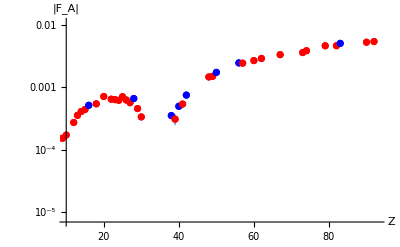

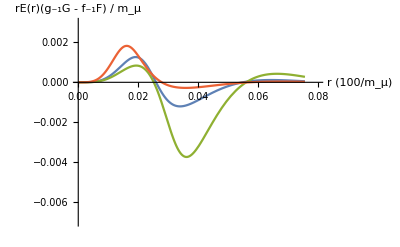

Z | F_A×10
9 | 1.530.07
10 | 1.730.04
12 | 2.750.25
13 | 3.60.4
14 | 4.120.27
15 | 4.43287
16 | 5.180.20
18 | 5.460.10
20 | 7.20.4
22 | 6.490.31
23 | 6.390.35
24 | 6.20.4
25 | 7.110.13
26 | 6.300.13
27 | 5.70.4
28 | 6.650.21
29 | 4.60.4
30 | 3.380.20
38 | -3.540.28
39 | -3.10.6
40 | -5.000.21
41 | -5.40.5
42 | -7.550.19
48 | -14.730.10
49 | -15.10.9
50 | -17.430.09
56 | -24.7295
57 | -24.490.26
60 | -26.9570.032
62 | -29.130.17
67 | -33.5175
73 | -36.2523
74 | -38.71.1
79 | -46.50.6
82 | -46.70.4
83 | -50.830.12
90 | -53.10.4
92 | -54.40.5

```mathematica
(* FA plots and tables with uncertainty *)
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
FA$Integrand$mean=Transpose[Transpose[Total$List$N10$muLBisC][[8]]][[1]];
FA$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBisC][[9]]/.{x_,y_}->Around[x,y]};
ListLogPlot[{#}&/@Abs[FA$List],PlotStyle->PlotColors,PlotRange->{{10,93},{0.000007,0.011}}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","A"],StandardForm] <> "|" }]

Plot[{FA$Integrand$mean[[19]]/mmu,,FA$Integrand$mean[[34]]/mmu,5FA$Integrand$mean[[4]]/mmu},{r,0,0.08 inf},PlotRange->{{0,0.08},{-0.007,0.003}}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm] <> ToString[Superscript["E",2],StandardForm]<>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[FA$List/.{x_,y_}->{x,y*10^4},{"Z",ToString[Cross[Subscript["F","A"],Superscript["10","4"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

### other O.I. plots and tables with SD

```mathematica
(* D and other O.I. plots and tables with uncertainty *)
D$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBisC][[10]]/.{x_,y_}->Around[x,y]};
Sp$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBisC][[11]]/.{x_,y_}->Around[x,y]};
Vp$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBisC][[12]]/.{x_,y_}->Around[x,y]};
Sn$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBisC][[13]]/.{x_,y_}->Around[x,y]};
Vn$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBisC][[14]]/.{x_,y_}->Around[x,y]};

D$Plot=ListLinePlot[D$List,PlotMarkers->"+",PlotStyle->Black,PlotRange->All];
Sp$Plot=ListLinePlot[Sp$List,PlotMarkers->"x",PlotStyle->{Red,Dashed},PlotRange->All];
Vp$Plot=ListLinePlot[Vp$List,PlotMarkers->"✶",PlotStyle->{Blue,Dotted},PlotRange->All];
Sn$Plot=ListLinePlot[Sn$List,PlotMarkers->"□",PlotStyle->{Magenta,Dashed},PlotRange->All];
Vn$Plot=ListLinePlot[Vn$List,PlotMarkers->"■",PlotStyle->{Green,Dotted},PlotRange->All];
Show[D$Plot,Sp$Plot,Vp$Plot,Sn$Plot,Vn$Plot,PlotRange->{{0,100},All},AxesLabel->{"Z" , "Overlap Integrals ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}]

DSpVp$data={};
For[i=1,i≤Length[D$List],i++,
AppendTo[DSpVp$data,{D$List[[i]][[1]],D$List[[i]][[2]],D$List[[i]][[2]]/(8e),Sp$List[[i]][[2]],Vp$List[[i]][[2]],Sn$List[[i]][[2]],Vn$List[[i]][[2]]}]
]

Text@Grid[Prepend[DSpVp$data,{"Z","D ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")","D/(8e)~Vp~Sp",ToString[Subscript["S","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["S","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,12,12,12,12,12,12}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

Z | D (m_μ) | D/(8e)~Vp~Sp | S_p (m_μ) | V_p (m_μ) | S_n (m_μ) | V_n (m_μ)
9 | 0.017600.00022 | 0.007270.00009 | 0.007520.00010 | 0.007790.00010 | 0.008360.00011 | 0.008660.00011
10 | 0.021330.00012 | 0.008800.00005 | 0.009100.00005 | 0.009490.00005 | 0.009100.00005 | 0.009490.00005
12 | 0.03170.0008 | 0.013080.00034 | 0.01350.0004 | 0.01430.0004 | 0.01350.0004 | 0.01430.0004
13 | 0.03830.0012 | 0.01580.0005 | 0.01630.0006 | 0.01730.0006 | 0.01760.0006 | 0.01870.0006
14 | 0.04410.0008 | 0.018220.00033 | 0.01880.0004 | 0.02010.0004 | 0.01880.0004 | 0.02010.0004
15 | 0.0495211 | 0.0204415 | 0.021052 | 0.0226364 | 0.0224555 | 0.0241455
16 | 0.05770.0006 | 0.023810.00023 | 0.024550.00026 | 0.026550.00026 | 0.024550.00026 | 0.026550.00026
18 | 0.06660.0004 | 0.027510.00016 | 0.028100.00017 | 0.030910.00018 | 0.034340.00021 | 0.037780.00022
20 | 0.08260.0011 | 0.03410.0005 | 0.03470.0005 | 0.03860.0005 | 0.03470.0005 | 0.03860.0005
22 | 0.09050.0009 | 0.03740.0004 | 0.03760.0004 | 0.04280.0004 | 0.04450.0005 | 0.05050.0005
23 | 0.09560.0012 | 0.03950.0005 | 0.03960.0006 | 0.04540.0006 | 0.04820.0007 | 0.05530.0007
24 | 0.10000.0016 | 0.04130.0006 | 0.04120.0007 | 0.04770.0007 | 0.04810.0008 | 0.05560.0009
25 | 0.10840.0004 | 0.044740.00017 | 0.044620.00018 | 0.051950.00019 | 0.053540.00022 | 0.062340.00023
26 | 0.11010.0005 | 0.045460.00021 | 0.045040.00022 | 0.053070.00024 | 0.051970.00026 | 0.061230.00027
27 | 0.11330.0014 | 0.04680.0006 | 0.04610.0006 | 0.05490.0007 | 0.05460.0007 | 0.06500.0008
28 | 0.12970.0007 | 0.053540.00028 | 0.052720.00031 | 0.063180.00032 | 0.056490.00033 | 0.067700.00034
29 | 0.11910.0018 | 0.04920.0007 | 0.04790.0008 | 0.05830.0008 | 0.05620.0009 | 0.06840.0010
30 | 0.11770.0009 | 0.04860.0004 | 0.04700.0004 | 0.05800.0004 | 0.05320.0004 | 0.06580.0005
38 | 0.14190.0013 | 0.05860.0005 | 0.05380.0006 | 0.07370.0006 | 0.07070.0008 | 0.09700.0008
39 | 0.1380.004 | 0.05690.0017 | 0.05230.0017 | 0.07200.0020 | 0.06700.0022 | 0.09230.0026
40 | 0.14530.0010 | 0.06000.0004 | 0.05450.0004 | 0.07650.0005 | 0.06810.0006 | 0.09560.0006
41 | 0.13700.0029 | 0.05650.0012 | 0.05120.0012 | 0.07280.0014 | 0.06490.0015 | 0.09230.0018
42 | 0.14000.0011 | 0.05780.0004 | 0.05150.0004 | 0.07510.0005 | 0.06870.0006 | 0.10010.0007
48 | 0.11830.0016 | 0.04890.0007 | 0.04140.0007 | 0.06820.0008 | 0.05690.0009 | 0.09370.0011
49 | 0.1350.010 | 0.0560.004 | 0.0470.004 | 0.0770.005 | 0.0640.005 | 0.1040.006
50 | 0.12910.0006 | 0.053310.00026 | 0.044330.00026 | 0.075130.00030 | 0.06210.0004 | 0.10520.0004
56 | 0.119402 | 0.0492871 | 0.0382777 | 0.0747934 | 0.0560495 | 0.109519
57 | 0.1120.005 | 0.04610.0019 | 0.03580.0018 | 0.07120.0024 | 0.05150.0026 | 0.10250.0034
60 | 0.117330.00017 | 0.048430.00007 | 0.036680.00006 | 0.076020.00010 | 0.050130.00009 | 0.103890.00013
62 | 0.11070.0007 | 0.045680.00031 | 0.033550.00027 | 0.07420.0004 | 0.04870.0004 | 0.10760.0006
67 | 0.0918782 | 0.0379258 | 0.0252038 | 0.0682134 | 0.0368652 | 0.0997749
73 | 0.0749307 | 0.0309302 | 0.0175478 | 0.0631594 | 0.0259612 | 0.0934412
74 | 0.0710.005 | 0.02950.0019 | 0.01610.0016 | 0.06270.0025 | 0.02390.0023 | 0.0930.004
79 | 0.0880.004 | 0.03640.0016 | 0.01960.0014 | 0.07590.0020 | 0.02930.0021 | 0.11340.0030
82 | 0.07310.0019 | 0.03020.0008 | 0.01400.0006 | 0.06970.0010 | 0.02140.0010 | 0.10720.0016
83 | 0.07690.0025 | 0.03170.0010 | 0.01390.0008 | 0.07420.0011 | 0.02110.0013 | 0.11260.0017
90 | 0.07030.0005 | 0.029030.00021 | 0.010450.00014 | 0.07400.0004 | 0.016480.00022 | 0.11680.0006
92 | 0.07140.0007 | 0.029460.00028 | 0.010060.00018 | 0.07580.0005 | 0.015970.00028 | 0.12030.0009

## Nreps = 10, muon lower bound is 3c

### Rho plots no SD, RMS table with SD, rho params table with SD

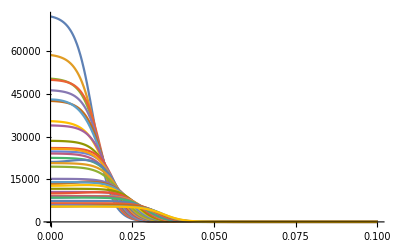

```mathematica
(* All rho plots *)
rho$mean = Transpose[Transpose[Total$List$N10$muLBis3C][[1]]][[1]];
Plot[rho$mean,{r,0,0.1},PlotRange->All]
```

```mathematica
(* RMS table *)
(* Units of fm (for comparison) *)
r$rms=Transpose@{Z$List,Transpose[Total$List$N10$muLBis3C][[2]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[r$rms,{"Z",ToString[Subscript["r","rms"],StandardForm]<>" (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | r_rms (fm)
9 | 2.8750.032
10 | 3.0330.017
12 | 3.110.09
13 | 3.050.08
14 | 3.170.05
15 | 3.2427
16 | 3.2380.014
18 | 3.4760.020
20 | 3.430.05
22 | 3.5850.026
23 | 3.5820.035
24 | 3.6580.029
25 | 3.6790.008
26 | 3.7840.010
27 | 3.8100.027
28 | 3.7560.007
29 | 3.900.04
30 | 4.0470.012
38 | 4.2630.009
39 | 4.240.06
40 | 4.2800.012
41 | 4.340.09
42 | 4.4220.008
48 | 4.6440.017
49 | 4.510.10
50 | 4.6490.005
56 | 4.83707
57 | 4.840.07
60 | 4.9100.004
62 | 4.9840.030
67 | 5.19249
73 | 5.48473
74 | 5.460.07
79 | 5.350.06
82 | 5.5160.033
83 | 5.5070.027
90 | 5.6590.014
92 | 5.7340.019

```mathematica
(* c, z, and w param tables *)
rho$params=Transpose@{Z$List,Transpose[Total$List$N10$muLBis3C][[3]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N10$muLBisC][[4]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N10$muLBisC][[5]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[rho$params,{"Z","c (fm)","z (fm)","w (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | c (fm) | z (fm) | w (fm)
9 | 2.5870.034 | 0.5620.014 | 0
10 | 2.8060.012 | 0.57250.0033 | 0
12 | 3.0040.027 | 0.5530.031 | 0
13 | 3.060.10 | 0.5240.020 | 0
14 | 3.1140.019 | 0.5460.016 | 0
15 | 3.21 | 0.56 | 0
16 | 2.540.11 | 2.1930.009 | 0.1620.015
18 | 3.3930.012 | 0.6130.008 | 0
20 | 3.510.08 | 0.563 | 0
22 | 3.740.04 | 0.567 | 0
23 | 3.9280.034 | 0.5040.014 | 0
24 | 3.9810.031 | 0.5300.015 | 0
25 | 3.8930.013 | 0.567 | 0
26 | 3.9670.011 | 0.5930.004 | 0
27 | 4.090.04 | 0.569 | 0
28 | 3.5970.012 | 2.31090.0034 | 0.3980.016
29 | 4.2210.034 | 0.5730.018 | 0
30 | 4.2690.014 | 0.6260.004 | 0
38 | 4.2520.013 | 2.5450.007 | 0.4730.035
39 | 4.730.05 | 0.5670.027 | 0
40 | 4.4450.015 | 2.52890.0033 | 0.3560.021
41 | 4.860.06 | 0.5680.021 | 0
42 | 4.5630.009 | 2.64870.0029 | 0.2960.018
48 | 5.4180.014 | 0.5370.010 | 0
49 | 5.230.09 | 0.520.06 | 0
50 | 5.1120.005 | 2.61690.0022 | 0.2910.014
56 | 5.3376 | 2.6776 | 0.3749
57 | 5.700.07 | 0.5290.019 | 0
60 | 5.6838 | 0.58700.0019 | 0
62 | 5.8044 | 0.5800.009 | 0
67 | 6.12 | 0.57 | 0
73 | 6.38 | 0.64 | 0
74 | 6.550.07 | 0.530.04 | 0
79 | 6.400.06 | 0.5380.021 | 0
82 | 6.620.04 | 0.5480.009 | 0
83 | 6.3100.008 | 2.8800.009 | 0.390.05
90 | 6.7915 | 0.5750.011 | 0
92 | 6.8054 | 0.6020.014 | 0

### E-field and potential plots with no SD

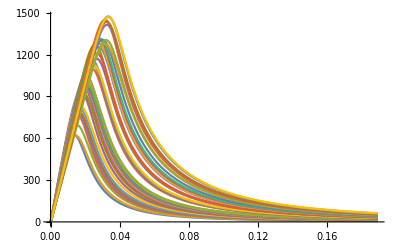

```mathematica
(* All E-field plots *)
Ef$mean = Transpose[Transpose[Total$List$N10$muLBis3C][[6]]][[1]];
Plot[Ef$mean,{r,0,0.2 inf},PlotRange->All]
```

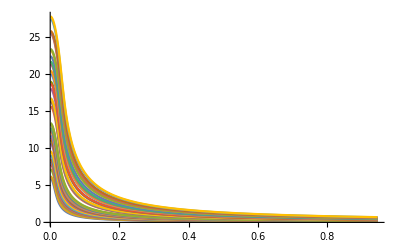

```mathematica
(* All potential plots *)
V$mean = Transpose[Transpose[Total$List$N10$muLBis3C][[7]]][[1]];
Plot[V$mean,{r,eps,inf},PlotRange->All]
```

### e.w.f. and m.w.f plots

```mathematica
(* All e.w.f. plots *)
u1$e$List=Transpose[Transpose[Total$List$N10$muLBis3C][[15]]][[1]];
u2$e$List=Transpose[Transpose[Total$List$N10$muLBis3C][[16]]][[1]];
u1$e$Plot=Plot[u1$e$List,{r,0,inf},PlotRange->All];
u2$e$Plot=Plot[u2$e$List,{r,0,inf},PlotRange->All];
Show[u1$e$Plot,u2$e$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Subscript["g",-1],StandardForm] <>", "<>ToString[Subscript["f",-1],StandardForm] }]
```

-Graphics-

```mathematica
(* All m.w.f. plots *)
u1$mu$List=Transpose[Transpose[Total$List$N10$muLBis3C][[17]]][[1]];
u2$mu$List=Transpose[Transpose[Total$List$N10$muLBis3C][[18]]][[1]];
u1$mu$Plot=Plot[u1$mu$List,{r,0,inf},PlotRange->All];
u2$mu$Plot=Plot[u2$mu$Plot,{r,0,inf},PlotRange->All];
Show[u1$mu$Plot,u2$mu$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F "<>ToString[Superscript["(MeV)","(1/2)"],StandardForm] }]
```

-Graphics-

```mathematica
(* Some m.w.f. plots with uncertainty *)
Plot[{u1$mu$List[[4]]/Sqrt[mmu],u2$mu$List[[4]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Al)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[10]]/Sqrt[mmu],u2$mu$List[[10]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Ti)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[34]]/Sqrt[mmu],u2$mu$List[[34]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Au)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
```

-Graphics-

-Graphics-

-Graphics-

### FA plots (with and without SD) and tables with SD

```mathematica
(* FA plots and tables with uncertainty *)
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
FA$Integrand$mean=Transpose[Transpose[Total$List$N10$muLBis3C][[8]]][[1]];
FA$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis3C][[9]]/.{x_,y_}->Around[x,y]};
ListLogPlot[{#}&/@Abs[FA$List],PlotStyle->PlotColors,PlotRange->{{10,93},{0.000007,0.011}}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","A"],StandardForm] <> "|" }]

Plot[{FA$Integrand$mean[[19]]/mmu,,FA$Integrand$mean[[34]]/mmu,5FA$Integrand$mean[[4]]/mmu},{r,0,0.08 inf},PlotRange->{{0,0.08},{-0.007,0.003}}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm] <> ToString[Superscript["E",2],StandardForm]<>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[FA$List/.{x_,y_}->{x,y*10^4},{"Z",ToString[Cross[Subscript["F","A"],Superscript["10","4"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

-Graphics-

Z | F_A×10
9 | 1.550.06
10 | 1.7520.034
12 | 2.740.28
13 | 3.70.4
14 | 4.050.23
15 | 4.43287
16 | 5.320.14
18 | 5.420.12
20 | 7.20.7
22 | 6.60.4
23 | 6.480.34
24 | 6.20.4
25 | 7.140.15
26 | 6.270.12
27 | 5.70.5
28 | 6.570.17
29 | 4.70.5
30 | 3.360.15
38 | -3.530.14
39 | -2.90.7
40 | -5.000.26
41 | -5.40.7
42 | -7.610.15
48 | -14.880.08
49 | -14.60.9
50 | -17.470.09
56 | -24.7295
57 | -24.40.6
60 | -26.990.04
62 | -29.10.4
67 | -33.5175
73 | -36.2523
74 | -38.31.0
79 | -46.60.8
82 | -46.70.5
83 | -50.850.13
90 | -53.50.4
92 | -54.20.5

### other O.I. plots and tables with SD

```mathematica
(* D and other O.I. plots and tables with uncertainty *)
D$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis3C][[10]]/.{x_,y_}->Around[x,y]};
Sp$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis3C][[11]]/.{x_,y_}->Around[x,y]};
Vp$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis3C][[12]]/.{x_,y_}->Around[x,y]};
Sn$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis3C][[13]]/.{x_,y_}->Around[x,y]};
Vn$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis3C][[14]]/.{x_,y_}->Around[x,y]};

D$Plot=ListLinePlot[D$List,PlotMarkers->"+",PlotStyle->Black,PlotRange->All];
Sp$Plot=ListLinePlot[Sp$List,PlotMarkers->"x",PlotStyle->{Red,Dashed},PlotRange->All];
Vp$Plot=ListLinePlot[Vp$List,PlotMarkers->"✶",PlotStyle->{Blue,Dotted},PlotRange->All];
Sn$Plot=ListLinePlot[Sn$List,PlotMarkers->"□",PlotStyle->{Magenta,Dashed},PlotRange->All];
Vn$Plot=ListLinePlot[Vn$List,PlotMarkers->"■",PlotStyle->{Green,Dotted},PlotRange->All];
Show[D$Plot,Sp$Plot,Vp$Plot,Sn$Plot,Vn$Plot,PlotRange->{{0,100},All},AxesLabel->{"Z" , "Overlap Integrals ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}]

DSpVp$data={};
For[i=1,i≤Length[D$List],i++,
AppendTo[DSpVp$data,{D$List[[i]][[1]],D$List[[i]][[2]],D$List[[i]][[2]]/(8e),Sp$List[[i]][[2]],Vp$List[[i]][[2]],Sn$List[[i]][[2]],Vn$List[[i]][[2]]}]
]

Text@Grid[Prepend[DSpVp$data,{"Z","D ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")","D/(8e)~Vp~Sp",ToString[Subscript["S","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["S","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,12,12,12,12,12,12}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

Z | D (m_μ) | D/(8e)~Vp~Sp | S_p (m_μ) | V_p (m_μ) | S_n (m_μ) | V_n (m_μ)
9 | 0.017650.00017 | 0.007290.00007 | 0.007550.00008 | 0.007810.00008 | 0.008380.00009 | 0.008680.00009
10 | 0.021410.00012 | 0.008840.00005 | 0.009130.00005 | 0.009530.00005 | 0.009130.00005 | 0.009530.00005
12 | 0.03160.0009 | 0.01310.0004 | 0.01350.0004 | 0.01420.0004 | 0.01350.0004 | 0.01420.0004
13 | 0.03860.0011 | 0.01590.0004 | 0.01650.0005 | 0.01750.0005 | 0.01780.0005 | 0.01880.0005
14 | 0.04390.0008 | 0.018120.00032 | 0.018710.00035 | 0.019970.00035 | 0.018710.00035 | 0.019970.00035
15 | 0.0495211 | 0.0204415 | 0.021052 | 0.0226364 | 0.0224555 | 0.0241455
16 | 0.05800.0004 | 0.023960.00015 | 0.024720.00017 | 0.026720.00017 | 0.024720.00017 | 0.026720.00017
18 | 0.06650.0005 | 0.027460.00019 | 0.028040.00020 | 0.030850.00021 | 0.034270.00025 | 0.037710.00026
20 | 0.08270.0019 | 0.03410.0008 | 0.03480.0009 | 0.03870.0009 | 0.03480.0009 | 0.03870.0009
22 | 0.09100.0012 | 0.03760.0005 | 0.03790.0005 | 0.04300.0005 | 0.04470.0006 | 0.05080.0006
23 | 0.09580.0013 | 0.03960.0005 | 0.03970.0006 | 0.04550.0006 | 0.04830.0007 | 0.05540.0007
24 | 0.09990.0013 | 0.04120.0005 | 0.04120.0006 | 0.04770.0006 | 0.04800.0007 | 0.05560.0007
25 | 0.10850.0005 | 0.044770.00019 | 0.044660.00021 | 0.051990.00022 | 0.053590.00025 | 0.062380.00026
26 | 0.11000.0005 | 0.045400.00020 | 0.044990.00021 | 0.053010.00022 | 0.051910.00024 | 0.061160.00026
27 | 0.11330.0017 | 0.04680.0007 | 0.04610.0008 | 0.05490.0008 | 0.05460.0009 | 0.06510.0009
28 | 0.12950.0005 | 0.053440.00022 | 0.052610.00024 | 0.063070.00025 | 0.056370.00026 | 0.067580.00027
29 | 0.11960.0022 | 0.04940.0009 | 0.04810.0010 | 0.05860.0010 | 0.05640.0011 | 0.06870.0012
30 | 0.11760.0007 | 0.048530.00028 | 0.046900.00029 | 0.057980.00031 | 0.053150.00033 | 0.06570.0004
38 | 0.14190.0008 | 0.058550.00032 | 0.053750.00034 | 0.07370.0004 | 0.07070.0004 | 0.09700.0005
39 | 0.1390.004 | 0.05720.0018 | 0.05260.0018 | 0.07240.0021 | 0.06750.0023 | 0.09280.0027
40 | 0.14530.0012 | 0.06000.0005 | 0.05450.0005 | 0.07650.0006 | 0.06810.0007 | 0.09560.0007
41 | 0.1360.006 | 0.05620.0025 | 0.05090.0026 | 0.07240.0030 | 0.06460.0033 | 0.0920.004
42 | 0.13960.0008 | 0.057620.00034 | 0.051350.00035 | 0.07490.0004 | 0.06850.0005 | 0.09980.0005
48 | 0.11700.0012 | 0.04830.0005 | 0.04080.0005 | 0.06750.0006 | 0.05610.0007 | 0.09290.0008
49 | 0.1370.008 | 0.05660.0034 | 0.04840.0034 | 0.0780.004 | 0.0650.005 | 0.1050.006
50 | 0.12860.0006 | 0.053100.00026 | 0.044130.00026 | 0.074890.00030 | 0.06180.0004 | 0.10490.0004
56 | 0.119402 | 0.0492871 | 0.0382777 | 0.0747934 | 0.0560495 | 0.109519
57 | 0.1130.006 | 0.04680.0023 | 0.03640.0021 | 0.07190.0028 | 0.05230.0031 | 0.1030.004
60 | 0.117510.00024 | 0.048510.00010 | 0.036750.00009 | 0.076120.00013 | 0.050220.00012 | 0.104030.00018
62 | 0.11080.0016 | 0.04570.0006 | 0.03360.0006 | 0.07420.0009 | 0.04870.0008 | 0.10770.0013
67 | 0.0918782 | 0.0379258 | 0.0252038 | 0.0682134 | 0.0368652 | 0.0997749
73 | 0.0749307 | 0.0309302 | 0.0175478 | 0.0631594 | 0.0259612 | 0.0934412
74 | 0.0690.004 | 0.02860.0018 | 0.01530.0015 | 0.06150.0024 | 0.02270.0023 | 0.0910.004
79 | 0.0890.005 | 0.03660.0020 | 0.01980.0016 | 0.07620.0026 | 0.02960.0025 | 0.1140.004
82 | 0.07350.0028 | 0.03030.0012 | 0.01410.0009 | 0.07000.0015 | 0.02170.0014 | 0.10750.0023
83 | 0.0790.004 | 0.03250.0015 | 0.01450.0013 | 0.07500.0017 | 0.02210.0019 | 0.11390.0027
90 | 0.07090.0005 | 0.029290.00020 | 0.010610.00013 | 0.07450.0004 | 0.016740.00021 | 0.11760.0006
92 | 0.07110.0006 | 0.029350.00026 | 0.009990.00017 | 0.07560.0005 | 0.015860.00027 | 0.12000.0008

## Nreps = 10, muon lower bound is 5c

### Rho plots no SD, RMS table with SD, rho params table with SD

```mathematica
(* All rho plots *)
rho$mean = Transpose[Transpose[Total$List$N10$muLBis5C][[1]]][[1]];
Plot[rho$mean,{r,0,0.1},PlotRange->All]
```

-Graphics-

```mathematica
(* RMS table *)
(* Units of fm (for comparison) *)
r$rms=Transpose@{Z$List,Transpose[Total$List$N10$muLBis5C][[2]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[r$rms,{"Z",ToString[Subscript["r","rms"],StandardForm]<>" (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | r_rms (fm)
9 | 2.8820.023
10 | 3.0290.014
12 | 3.090.08
13 | 3.060.09
14 | 3.1230.035
15 | 3.2427
16 | 3.2430.017
18 | 3.4930.031
20 | 3.440.05
22 | 3.5890.020
23 | 3.570.04
24 | 3.6620.030
25 | 3.6770.007
26 | 3.7850.011
27 | 3.810.05
28 | 3.7660.005
29 | 3.930.05
30 | 4.0440.016
38 | 4.2620.012
39 | 4.210.06
40 | 4.2760.008
41 | 4.350.05
42 | 4.4220.010
48 | 4.6370.018
49 | 4.530.05
50 | 4.6470.005
56 | 4.83707
57 | 4.840.06
60 | 4.9120.004
62 | 5.0060.025
67 | 5.19249
73 | 5.48473
74 | 5.440.06
79 | 5.340.04
82 | 5.5330.028
83 | 5.5290.022
90 | 5.6730.018
92 | 5.7370.027

```mathematica
(* c, z, and w param tables *)
rho$params=Transpose@{Z$List,Transpose[Total$List$N10$muLBis5C][[3]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N10$muLBis5C][[4]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N10$muLBis5C][[5]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[rho$params,{"Z","c (fm)","z (fm)","w (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | c (fm) | z (fm) | w (fm)
9 | 2.5900.028 | 0.5570.007 | 0
10 | 2.8060.019 | 0.56780.0029 | 0
12 | 2.980.06 | 0.5530.033 | 0
13 | 3.070.11 | 0.5190.026 | 0
14 | 3.0960.020 | 0.5380.012 | 0
15 | 3.21 | 0.56 | 0
16 | 2.510.11 | 2.1970.008 | 0.1610.010
18 | 3.3910.018 | 0.6190.013 | 0
20 | 3.520.08 | 0.563 | 0
22 | 3.7500.032 | 0.567 | 0
23 | 3.9410.031 | 0.5000.012 | 0
24 | 3.9890.023 | 0.5290.010 | 0
25 | 3.8890.011 | 0.567 | 0
26 | 3.9670.009 | 0.5950.004 | 0
27 | 4.100.07 | 0.569 | 0
28 | 3.6040.008 | 2.31160.0019 | 0.4290.015
29 | 4.2200.023 | 0.5850.023 | 0
30 | 4.2650.021 | 0.6280.004 | 0
38 | 4.2630.010 | 2.5470.006 | 0.4590.031
39 | 4.760.05 | 0.5490.028 | 0
40 | 4.4290.016 | 2.52800.0012 | 0.3610.018
41 | 4.870.05 | 0.5790.030 | 0
42 | 4.5520.013 | 2.6500.004 | 0.3020.024
48 | 5.3990.019 | 0.5390.007 | 0
49 | 5.190.11 | 0.5650.034 | 0
50 | 5.1130.005 | 2.61830.0021 | 0.2920.014
56 | 5.3376 | 2.6776 | 0.3749
57 | 5.700.05 | 0.5350.032 | 0
60 | 5.6838 | 0.58620.0024 | 0
62 | 5.8044 | 0.5920.015 | 0
67 | 6.12 | 0.57 | 0
73 | 6.38 | 0.64 | 0
74 | 6.520.04 | 0.540.04 | 0
79 | 6.380.04 | 0.5440.026 | 0
82 | 6.6330.035 | 0.5520.006 | 0
83 | 6.3160.007 | 2.8820.007 | 0.410.06
90 | 6.7915 | 0.5710.013 | 0
92 | 6.8054 | 0.6090.018 | 0

### E-field and potential plots with no SD

```mathematica
(* All E-field plots *)
Ef$mean = Transpose[Transpose[Total$List$N10$muLBis5C][[6]]][[1]];
Plot[Ef$mean,{r,0,0.2 inf},PlotRange->All]
```

-Graphics-

```mathematica
(* All potential plots *)
V$mean = Transpose[Transpose[Total$List$N10$muLBis5C][[7]]][[1]];
Plot[V$mean,{r,eps,inf},PlotRange->All]
```

-Graphics-

### e.w.f. and m.w.f plots

```mathematica
(* All e.w.f. plots *)
u1$e$List=Transpose[Transpose[Total$List$N10$muLBis5C][[15]]][[1]];
u2$e$List=Transpose[Transpose[Total$List$N10$muLBis5C][[16]]][[1]];
u1$e$Plot=Plot[u1$e$List,{r,0,inf},PlotRange->All];
u2$e$Plot=Plot[u2$e$List,{r,0,inf},PlotRange->All];
Show[u1$e$Plot,u2$e$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Subscript["g",-1],StandardForm] <>", "<>ToString[Subscript["f",-1],StandardForm] }]
```

-Graphics-

```mathematica
(* All m.w.f. plots *)
u1$mu$List=Transpose[Transpose[Total$List$N10$muLBis5C][[17]]][[1]];
u2$mu$List=Transpose[Transpose[Total$List$N10$muLBis5C][[18]]][[1]];
u1$mu$Plot=Plot[u1$mu$List,{r,0,inf},PlotRange->All];
u2$mu$Plot=Plot[u2$mu$List,{r,0,inf},PlotRange->All];
Show[u1$mu$Plot,u2$mu$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F "<>ToString[Superscript["(MeV)","(1/2)"],StandardForm] }]
```

-Graphics-

```mathematica
(* Some m.w.f. plots with uncertainty *)
Plot[{u1$mu$List[[4]]/Sqrt[mmu],u2$mu$List[[4]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Al)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[10]]/Sqrt[mmu],u2$mu$List[[10]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Ti)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[34]]/Sqrt[mmu],u2$mu$List[[34]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Au)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
```

-Graphics-

-Graphics-

-Graphics-

### FA plots (with and without SD) and tables with SD

```mathematica
(* FA plots and tables with uncertainty *)
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
FA$Integrand$mean=Transpose[Transpose[Total$List$N10$muLBis5C][[8]]][[1]];
FA$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis5C][[9]]/.{x_,y_}->Around[x,y]};
ListLogPlot[{#}&/@Abs[FA$List],PlotStyle->PlotColors,PlotRange->{{10,93},{0.000007,0.011}}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","A"],StandardForm] <> "|" }]

Plot[{FA$Integrand$mean[[19]]/mmu,,FA$Integrand$mean[[34]]/mmu,5FA$Integrand$mean[[4]]/mmu},{r,0,0.08 inf},PlotRange->{{0,0.08},{-0.007,0.003}}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm] <> ToString[Superscript["E",2],StandardForm]<>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[FA$List/.{x_,y_}->{x,y*10^4},{"Z",ToString[Cross[Subscript["F","A"],Superscript["10","4"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

-Graphics-

Z | F_A×10
9 | 1.530.04
10 | 1.7580.033
12 | 2.810.23
13 | 3.60.5
14 | 4.260.18
15 | 4.43287
16 | 5.290.17
18 | 5.320.20
20 | 7.10.7
22 | 6.580.29
23 | 6.50.4
24 | 6.120.35
25 | 7.180.13
26 | 6.260.13
27 | 5.70.8
28 | 6.350.12
29 | 4.50.4
30 | 3.400.24
38 | -3.510.28
39 | -3.00.7
40 | -4.950.17
41 | -5.60.5
42 | -7.610.21
48 | -14.740.12
49 | -14.11.0
50 | -17.460.09
56 | -24.7295
57 | -24.40.5
60 | -26.970.04
62 | -28.890.29
67 | -33.5175
73 | -36.2523
74 | -38.61.1
79 | -46.50.8
82 | -46.40.4
83 | -50.750.12
90 | -53.20.5
92 | -54.10.7

### other O.I. plots and tables with SD

```mathematica
(* D and other O.I. plots and tables with uncertainty *)
D$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis5C][[10]]/.{x_,y_}->Around[x,y]};
Sp$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis5C][[11]]/.{x_,y_}->Around[x,y]};
Vp$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis5C][[12]]/.{x_,y_}->Around[x,y]};
Sn$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis5C][[13]]/.{x_,y_}->Around[x,y]};
Vn$List=Transpose@{Z$List,Transpose[Total$List$N10$muLBis5C][[14]]/.{x_,y_}->Around[x,y]};

D$Plot=ListLinePlot[D$List,PlotMarkers->"+",PlotStyle->Black,PlotRange->All];
Sp$Plot=ListLinePlot[Sp$List,PlotMarkers->"x",PlotStyle->{Red,Dashed},PlotRange->All];
Vp$Plot=ListLinePlot[Vp$List,PlotMarkers->"✶",PlotStyle->{Blue,Dotted},PlotRange->All];
Sn$Plot=ListLinePlot[Sn$List,PlotMarkers->"□",PlotStyle->{Magenta,Dashed},PlotRange->All];
Vn$Plot=ListLinePlot[Vn$List,PlotMarkers->"■",PlotStyle->{Green,Dotted},PlotRange->All];
Show[D$Plot,Sp$Plot,Vp$Plot,Sn$Plot,Vn$Plot,PlotRange->{{0,100},All},AxesLabel->{"Z" , "Overlap Integrals ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}]

DSpVp$data={};
For[i=1,i≤Length[D$List],i++,
AppendTo[DSpVp$data,{D$List[[i]][[1]],D$List[[i]][[2]],D$List[[i]][[2]]/(8e),Sp$List[[i]][[2]],Vp$List[[i]][[2]],Sn$List[[i]][[2]],Vn$List[[i]][[2]]}]
]

Text@Grid[Prepend[DSpVp$data,{"Z","D ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")","D/(8e)~Vp~Sp",ToString[Subscript["S","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["S","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,12,12,12,12,12,12}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

Z | D (m_μ) | D/(8e)~Vp~Sp | S_p (m_μ) | V_p (m_μ) | S_n (m_μ) | V_n (m_μ)
9 | 0.017620.00013 | 0.007270.00005 | 0.007530.00006 | 0.007800.00006 | 0.008370.00006 | 0.008670.00006
10 | 0.021430.00010 | 0.008850.00004 | 0.009150.00005 | 0.009540.00005 | 0.009150.00005 | 0.009540.00005
12 | 0.03190.0008 | 0.013160.00032 | 0.013600.00035 | 0.014340.00035 | 0.013600.00035 | 0.014340.00035
13 | 0.03850.0013 | 0.01590.0005 | 0.01640.0006 | 0.01740.0006 | 0.01770.0006 | 0.01870.0006
14 | 0.04450.0005 | 0.018380.00022 | 0.019000.00024 | 0.020260.00024 | 0.019000.00024 | 0.020260.00024
15 | 0.0495211 | 0.0204415 | 0.021052 | 0.0226364 | 0.0224555 | 0.0241455
16 | 0.05790.0004 | 0.023920.00018 | 0.024670.00021 | 0.026680.00021 | 0.024670.00021 | 0.026680.00021
18 | 0.06610.0007 | 0.027300.00030 | 0.027870.00033 | 0.030680.00034 | 0.03410.0004 | 0.03750.0004
20 | 0.08240.0018 | 0.03400.0007 | 0.03460.0008 | 0.03860.0008 | 0.03460.0008 | 0.03860.0008
22 | 0.09080.0009 | 0.03750.0004 | 0.03780.0004 | 0.04290.0004 | 0.04460.0005 | 0.05070.0005
23 | 0.09600.0015 | 0.03960.0006 | 0.03980.0007 | 0.04560.0007 | 0.04840.0008 | 0.05550.0009
24 | 0.09970.0013 | 0.04110.0005 | 0.04110.0006 | 0.04760.0006 | 0.04790.0007 | 0.05550.0007
25 | 0.10860.0004 | 0.044830.00016 | 0.044720.00018 | 0.052050.00018 | 0.053660.00021 | 0.062460.00022
26 | 0.10990.0005 | 0.045380.00022 | 0.044970.00023 | 0.052980.00025 | 0.051880.00027 | 0.061130.00028
27 | 0.11310.0028 | 0.04670.0012 | 0.04600.0013 | 0.05480.0013 | 0.05450.0015 | 0.06500.0016
28 | 0.12880.0004 | 0.053150.00015 | 0.052290.00017 | 0.062740.00017 | 0.056020.00018 | 0.067220.00018
29 | 0.11820.0022 | 0.04880.0009 | 0.04750.0010 | 0.05790.0011 | 0.05570.0011 | 0.06790.0012
30 | 0.11780.0010 | 0.04860.0004 | 0.04700.0004 | 0.05810.0005 | 0.05320.0005 | 0.06580.0005
38 | 0.14200.0013 | 0.05860.0005 | 0.05380.0006 | 0.07380.0006 | 0.07080.0007 | 0.09710.0008
39 | 0.1400.004 | 0.05760.0017 | 0.05300.0018 | 0.07290.0020 | 0.06800.0023 | 0.09350.0026
40 | 0.14560.0008 | 0.060090.00033 | 0.054610.00035 | 0.07660.0004 | 0.06830.0004 | 0.09580.0005
41 | 0.13550.0034 | 0.05590.0014 | 0.05060.0014 | 0.07210.0016 | 0.06420.0018 | 0.09140.0021
42 | 0.13960.0011 | 0.05760.0004 | 0.05140.0005 | 0.07490.0005 | 0.06850.0006 | 0.09980.0007
48 | 0.11790.0014 | 0.04870.0006 | 0.04120.0006 | 0.06800.0007 | 0.05670.0008 | 0.09340.0010
49 | 0.1370.005 | 0.05640.0023 | 0.04820.0023 | 0.07770.0026 | 0.06490.0031 | 0.10470.0035
50 | 0.12880.0006 | 0.053170.00025 | 0.044200.00025 | 0.074970.00029 | 0.061870.00035 | 0.10500.0004
56 | 0.119402 | 0.0492871 | 0.0382777 | 0.0747934 | 0.0560495 | 0.109519
57 | 0.1130.005 | 0.04670.0019 | 0.03630.0018 | 0.07190.0023 | 0.05220.0025 | 0.10340.0034
60 | 0.117400.00021 | 0.048460.00009 | 0.036710.00008 | 0.076060.00012 | 0.050170.00011 | 0.103940.00016
62 | 0.10970.0013 | 0.04530.0005 | 0.03320.0005 | 0.07360.0007 | 0.04820.0007 | 0.10680.0011
67 | 0.0918782 | 0.0379258 | 0.0252038 | 0.0682134 | 0.0368652 | 0.0997749
73 | 0.0749307 | 0.0309302 | 0.0175478 | 0.0631594 | 0.0259612 | 0.0934412
74 | 0.07060.0029 | 0.02910.0012 | 0.01580.0010 | 0.06230.0017 | 0.02350.0015 | 0.09250.0026
79 | 0.08960.0027 | 0.03700.0011 | 0.02010.0009 | 0.07660.0015 | 0.03010.0013 | 0.11440.0022
82 | 0.07220.0023 | 0.02980.0010 | 0.01370.0008 | 0.06920.0012 | 0.02100.0012 | 0.10640.0019
83 | 0.07580.0028 | 0.03130.0012 | 0.01360.0010 | 0.07370.0013 | 0.02060.0015 | 0.11190.0020
90 | 0.07050.0006 | 0.029100.00025 | 0.010490.00017 | 0.07420.0005 | 0.016550.00026 | 0.11700.0008
92 | 0.07100.0009 | 0.02930.0004 | 0.009960.00023 | 0.07550.0007 | 0.01580.0004 | 0.11990.0011

## Nreps = 20, muon lower bound is 0.1c

### Rho plots no SD, RMS table with SD, rho params table with SD

```mathematica
(* All rho plots *)
rho$mean = Transpose[Transpose[Total$List$N20$muLBis01C][[1]]][[1]];
Plot[rho$mean,{r,0,0.1},PlotRange->All]
```

-Graphics-

```mathematica
(* RMS table *)
(* Units of fm (for comparison) *)
r$rms=Transpose@{Z$List,Transpose[Total$List$N20$muLBis01C][[2]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[r$rms,{"Z",ToString[Subscript["r","rms"],StandardForm]<>" (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | r_rms (fm)
9 | 2.8830.032
10 | 3.0430.010
12 | 3.060.10
13 | 3.070.06
14 | 3.140.04
15 | 3.2427
16 | 3.2410.026
18 | 3.4800.030
20 | 3.4440.028
22 | 3.5700.024
23 | 3.5870.031
24 | 3.6530.029
25 | 3.6760.009
26 | 3.7840.012
27 | 3.7960.027
28 | 3.7640.008
29 | 3.9080.028
30 | 4.0410.012
38 | 4.2670.012
39 | 4.240.06
40 | 4.2720.013
41 | 4.350.07
42 | 4.4230.008
48 | 4.6310.022
49 | 4.490.07
50 | 4.6440.007
56 | 4.83707
57 | 4.860.06
60 | 4.9150.004
62 | 4.9930.030
67 | 5.19249
73 | 5.48473
74 | 5.440.07
79 | 5.340.07
82 | 5.5190.027
83 | 5.5120.022
90 | 5.6650.020
92 | 5.7230.016

```mathematica
(* c, z, and w param tables *)
rho$params=Transpose@{Z$List,Transpose[Total$List$N20$muLBis01C][[3]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N20$muLBis01C][[4]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N20$muLBis01C][[5]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[rho$params,{"Z","c (fm)","z (fm)","w (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | c (fm) | z (fm) | w (fm)
9 | 2.5900.032 | 0.5570.011 | 0
10 | 2.8140.010 | 0.5710.004 | 0
12 | 2.990.06 | 0.540.04 | 0
13 | 3.060.06 | 0.5270.024 | 0
14 | 3.1020.027 | 0.5450.015 | 0
15 | 3.21 | 0.56 | 0
16 | 2.540.12 | 2.1920.014 | 0.1610.010
18 | 3.3880.010 | 0.6150.012 | 0
20 | 3.530.05 | 0.563 | 0
22 | 3.720.04 | 0.567 | 0
23 | 3.9380.022 | 0.5070.016 | 0
24 | 3.9730.028 | 0.5290.013 | 0
25 | 3.8890.015 | 0.567 | 0
26 | 3.9700.013 | 0.5930.004 | 0
27 | 4.070.04 | 0.569 | 0
28 | 3.6050.012 | 2.3120.005 | 0.4230.016
29 | 4.2140.032 | 0.5780.015 | 0
30 | 4.2630.016 | 0.62700.0029 | 0
38 | 4.2480.010 | 2.5500.005 | 0.4820.028
39 | 4.760.05 | 0.5630.028 | 0
40 | 4.4340.021 | 2.52840.0027 | 0.3420.020
41 | 4.890.05 | 0.5760.026 | 0
42 | 4.5600.016 | 2.64970.0026 | 0.2990.016
48 | 5.3990.024 | 0.5350.007 | 0
49 | 5.240.08 | 0.520.04 | 0
50 | 5.1090.007 | 2.61940.0035 | 0.2880.011
56 | 5.3376 | 2.6776 | 0.3749
57 | 5.710.06 | 0.5380.028 | 0
60 | 5.6838 | 0.58780.0026 | 0
62 | 5.8044 | 0.5840.019 | 0
67 | 6.12 | 0.57 | 0
73 | 6.38 | 0.64 | 0
74 | 6.520.07 | 0.5440.034 | 0
79 | 6.400.06 | 0.5340.031 | 0
82 | 6.6170.028 | 0.5510.011 | 0
83 | 6.3120.011 | 2.8800.006 | 0.370.05
90 | 6.7915 | 0.5650.014 | 0
92 | 6.8054 | 0.5990.011 | 0

### E-field and potential plots with no SD

```mathematica
(* All E-field plots *)
Ef$mean = Transpose[Transpose[Total$List$N20$muLBis01C][[6]]][[1]];
Plot[Ef$mean,{r,0,0.2 inf},PlotRange->All]
```

-Graphics-

```mathematica
(* All potential plots *)
V$mean = Transpose[Transpose[Total$List$N20$muLBis01C][[7]]][[1]];
Plot[V$mean,{r,eps,inf},PlotRange->All]
```

-Graphics-

### e.w.f. and m.w.f plots

```mathematica
(* All e.w.f. plots *)
u1$e$List=Transpose[Transpose[Total$List$N20$muLBis01C][[15]]][[1]];
u2$e$List=Transpose[Transpose[Total$List$N20$muLBis01C][[16]]][[1]];
u1$e$Plot=Plot[u1$e$List,{r,0,inf},PlotRange->All];
u2$e$Plot=Plot[u2$e$List,{r,0,inf},PlotRange->All];
Show[u1$e$Plot,u2$e$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Subscript["g",-1],StandardForm] <>", "<>ToString[Subscript["f",-1],StandardForm] }]
```

-Graphics-

```mathematica
(* All m.w.f. plots *)
u1$mu$List=Transpose[Transpose[Total$List$N20$muLBis01C][[17]]][[1]];
u2$mu$List=Transpose[Transpose[Total$List$N20$muLBis01C][[18]]][[1]];
u1$mu$Plot=Plot[u1$mu$List,{r,0,inf},PlotRange->All];
u2$mu$Plot=Plot[u2$mu$List,{r,0,inf},PlotRange->All];
Show[u1$mu$Plot,u2$mu$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F "<>ToString[Superscript["(MeV)","(1/2)"],StandardForm] }]
```

-Graphics-

```mathematica
(* Some m.w.f. plots with uncertainty *)
Plot[{u1$mu$List[[4]]/Sqrt[mmu],u2$mu$List[[4]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Al)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[10]]/Sqrt[mmu],u2$mu$List[[10]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Ti)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[34]]/Sqrt[mmu],u2$mu$List[[34]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Au)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
```

-Graphics-

-Graphics-

-Graphics-

### FA plots (with and without SD) and tables with SD

```mathematica
(* FA plots and tables with uncertainty *)
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
FA$Integrand$mean=Transpose[Transpose[Total$List$N20$muLBis01C][[8]]][[1]];
FA$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis01C][[9]]/.{x_,y_}->Around[x,y]};
ListLogPlot[{#}&/@Abs[FA$List],PlotStyle->PlotColors,PlotRange->{{10,93},{0.000007,0.011}}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","A"],StandardForm] <> "|" }]

Plot[{FA$Integrand$mean[[19]]/mmu,,FA$Integrand$mean[[34]]/mmu,5FA$Integrand$mean[[4]]/mmu},{r,0,0.08 inf},PlotRange->{{0,0.08},{-0.007,0.003}}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm] <> ToString[Superscript["E",2],StandardForm]<>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[FA$List/.{x_,y_}->{x,y*10^4},{"Z",ToString[Cross[Subscript["F","A"],Superscript["10","4"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

-Graphics-

Z | F_A×10
9 | 1.530.06
10 | 1.7300.020
12 | 2.930.33
13 | 3.610.25
14 | 4.170.18
15 | 4.43287
16 | 5.300.24
18 | 5.400.19
20 | 7.00.4
22 | 6.90.4
23 | 6.390.30
24 | 6.280.33
25 | 7.190.17
26 | 6.260.16
27 | 6.00.5
28 | 6.390.18
29 | 4.70.4
30 | 3.440.18
38 | -3.600.25
39 | -3.20.6
40 | -4.830.29
41 | -5.70.7
42 | -7.640.14
48 | -14.760.15
49 | -14.70.7
50 | -17.410.09
56 | -24.7295
57 | -24.30.4
60 | -26.940.04
62 | -29.00.4
67 | -33.5175
73 | -36.2523
74 | -38.51.0
79 | -46.71.2
82 | -46.60.5
83 | -50.840.17
90 | -53.40.5
92 | -54.50.4

### other O.I. plots and tables with SD

```mathematica
(* D and other O.I. plots and tables with uncertainty *)
D$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis01C][[10]]/.{x_,y_}->Around[x,y]};
Sp$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis01C][[11]]/.{x_,y_}->Around[x,y]};
Vp$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis01C][[12]]/.{x_,y_}->Around[x,y]};
Sn$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis01C][[13]]/.{x_,y_}->Around[x,y]};
Vn$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis01C][[14]]/.{x_,y_}->Around[x,y]};

D$Plot=ListLinePlot[D$List,PlotMarkers->"+",PlotStyle->Black,PlotRange->All];
Sp$Plot=ListLinePlot[Sp$List,PlotMarkers->"x",PlotStyle->{Red,Dashed},PlotRange->All];
Vp$Plot=ListLinePlot[Vp$List,PlotMarkers->"✶",PlotStyle->{Blue,Dotted},PlotRange->All];
Sn$Plot=ListLinePlot[Sn$List,PlotMarkers->"□",PlotStyle->{Magenta,Dashed},PlotRange->All];
Vn$Plot=ListLinePlot[Vn$List,PlotMarkers->"■",PlotStyle->{Green,Dotted},PlotRange->All];
Show[D$Plot,Sp$Plot,Vp$Plot,Sn$Plot,Vn$Plot,PlotRange->{{0,100},All},AxesLabel->{"Z" , "Overlap Integrals ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}]

DSpVp$data={};
For[i=1,i≤Length[D$List],i++,
AppendTo[DSpVp$data,{D$List[[i]][[1]],D$List[[i]][[2]],D$List[[i]][[2]]/(8e),Sp$List[[i]][[2]],Vp$List[[i]][[2]],Sn$List[[i]][[2]],Vn$List[[i]][[2]]}]
]

Text@Grid[Prepend[DSpVp$data,{"Z","D ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")","D/(8e)~Vp~Sp",ToString[Subscript["S","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["S","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,12,12,12,12,12,12}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

Z | D (m_μ) | D/(8e)~Vp~Sp | S_p (m_μ) | V_p (m_μ) | S_n (m_μ) | V_n (m_μ)
9 | 0.017610.00017 | 0.007270.00007 | 0.007530.00008 | 0.007800.00008 | 0.008360.00009 | 0.008660.00009
10 | 0.021340.00007 | 0.0088080.000029 | 0.0091020.000032 | 0.0094960.000032 | 0.0091020.000032 | 0.0094960.000032
12 | 0.03220.0010 | 0.01330.0004 | 0.01380.0005 | 0.01450.0005 | 0.01380.0005 | 0.01450.0005
13 | 0.03840.0007 | 0.015850.00030 | 0.016390.00033 | 0.017370.00033 | 0.017650.00035 | 0.01870.0004
14 | 0.04430.0006 | 0.018270.00023 | 0.018870.00026 | 0.020130.00026 | 0.018870.00026 | 0.020130.00026
15 | 0.0495211 | 0.0204415 | 0.021052 | 0.0226364 | 0.0224555 | 0.0241455
16 | 0.05800.0006 | 0.023940.00026 | 0.024690.00029 | 0.026700.00029 | 0.024690.00029 | 0.026700.00029
18 | 0.06640.0007 | 0.027430.00029 | 0.028010.00031 | 0.030820.00032 | 0.03420.0004 | 0.03770.0004
20 | 0.08220.0011 | 0.03390.0004 | 0.03450.0005 | 0.03850.0005 | 0.03450.0005 | 0.03850.0005
22 | 0.09160.0011 | 0.03780.0004 | 0.03820.0005 | 0.04330.0005 | 0.04510.0006 | 0.05120.0006
23 | 0.09560.0011 | 0.03950.0005 | 0.03960.0005 | 0.04540.0005 | 0.04820.0006 | 0.05520.0007
24 | 0.10010.0012 | 0.04130.0005 | 0.04130.0006 | 0.04780.0006 | 0.04820.0007 | 0.05570.0007
25 | 0.10860.0005 | 0.044830.00021 | 0.044730.00024 | 0.052060.00024 | 0.053670.00028 | 0.062470.00029
26 | 0.11000.0006 | 0.045390.00024 | 0.044980.00026 | 0.053000.00027 | 0.051890.00030 | 0.061150.00032
27 | 0.11420.0017 | 0.04710.0007 | 0.04650.0008 | 0.05530.0008 | 0.05510.0009 | 0.06560.0009
28 | 0.12890.0006 | 0.053190.00024 | 0.052340.00026 | 0.062790.00027 | 0.056070.00028 | 0.067270.00029
29 | 0.11920.0015 | 0.04920.0006 | 0.04800.0007 | 0.05840.0007 | 0.05620.0008 | 0.06850.0008
30 | 0.11790.0008 | 0.048670.00032 | 0.047050.00034 | 0.05810.0004 | 0.05330.0004 | 0.06590.0004
38 | 0.14150.0012 | 0.05840.0005 | 0.05360.0005 | 0.07350.0006 | 0.07050.0007 | 0.09680.0007
39 | 0.1380.004 | 0.05680.0016 | 0.05220.0017 | 0.07200.0019 | 0.06700.0022 | 0.09220.0025
40 | 0.14610.0014 | 0.06030.0006 | 0.05480.0006 | 0.07690.0006 | 0.06850.0007 | 0.09610.0008
41 | 0.1350.005 | 0.05570.0020 | 0.05030.0021 | 0.07170.0024 | 0.06380.0026 | 0.09100.0030
42 | 0.13950.0008 | 0.057570.00033 | 0.051300.00034 | 0.07480.0004 | 0.06840.0005 | 0.09970.0005
48 | 0.11830.0018 | 0.04880.0007 | 0.04130.0007 | 0.06810.0009 | 0.05680.0010 | 0.09370.0012
49 | 0.1380.006 | 0.05680.0023 | 0.04850.0022 | 0.07840.0027 | 0.06540.0030 | 0.1060.004
50 | 0.12920.0008 | 0.053320.00031 | 0.044350.00031 | 0.07510.0004 | 0.06210.0004 | 0.10520.0005
56 | 0.119402 | 0.0492871 | 0.0382777 | 0.0747934 | 0.0560495 | 0.109519
57 | 0.1120.005 | 0.04640.0020 | 0.03600.0019 | 0.07150.0025 | 0.05180.0027 | 0.1030.004
60 | 0.117260.00023 | 0.048400.00010 | 0.036660.00009 | 0.075980.00013 | 0.050100.00012 | 0.103840.00018
62 | 0.11030.0015 | 0.04550.0006 | 0.03340.0006 | 0.07390.0009 | 0.04850.0008 | 0.10730.0013
67 | 0.0918782 | 0.0379258 | 0.0252038 | 0.0682134 | 0.0368652 | 0.0997749
73 | 0.0749307 | 0.0309302 | 0.0175478 | 0.0631594 | 0.0259612 | 0.0934412
74 | 0.0710.005 | 0.02920.0019 | 0.01590.0016 | 0.06230.0025 | 0.02360.0024 | 0.0930.004
79 | 0.0890.005 | 0.03680.0021 | 0.02000.0017 | 0.07640.0028 | 0.02980.0025 | 0.1140.004
82 | 0.07330.0020 | 0.03030.0008 | 0.01410.0007 | 0.06990.0011 | 0.02160.0010 | 0.10730.0017
83 | 0.07790.0028 | 0.03220.0012 | 0.01430.0010 | 0.07470.0014 | 0.02170.0015 | 0.11340.0021
90 | 0.07080.0007 | 0.029210.00027 | 0.010570.00018 | 0.07440.0005 | 0.016670.00028 | 0.11740.0008
92 | 0.07150.0005 | 0.029510.00022 | 0.010090.00014 | 0.07590.0004 | 0.016010.00023 | 0.12050.0007

## Nreps = 20, muon lower bound is 0.5c

### Rho plots no SD, RMS table with SD, rho params table with SD

```mathematica
(* All rho plots *)
rho$mean = Transpose[Transpose[Total$List$N20$muLBis05C][[1]]][[1]];
Plot[rho$mean,{r,0,0.1},PlotRange->All]
```

-Graphics-

```mathematica
(* RMS table *)
(* Units of fm (for comparison) *)
r$rms=Transpose@{Z$List,Transpose[Total$List$N20$muLBis05C][[2]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[r$rms,{"Z",ToString[Subscript["r","rms"],StandardForm]<>" (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | r_rms (fm)
9 | 2.900.05
10 | 3.0390.014
12 | 3.090.09
13 | 3.060.07
14 | 3.1500.033
15 | 3.2427
16 | 3.2390.019
18 | 3.4690.027
20 | 3.410.05
22 | 3.5880.030
23 | 3.5790.031
24 | 3.6500.027
25 | 3.6790.008
26 | 3.7820.013
27 | 3.8070.031
28 | 3.7610.008
29 | 3.920.04
30 | 4.0360.011
38 | 4.2620.012
39 | 4.240.05
40 | 4.2750.013
41 | 4.340.05
42 | 4.4240.010
48 | 4.6290.017
49 | 4.530.10
50 | 4.6460.006
56 | 4.83707
57 | 4.850.06
60 | 4.9140.005
62 | 4.9880.019
67 | 5.19249
73 | 5.48473
74 | 5.450.06
79 | 5.320.05
82 | 5.5280.024
83 | 5.5220.019
90 | 5.6640.017
92 | 5.7270.029

```mathematica
(* c, z, and w param tables *)
rho$params=Transpose@{Z$List,Transpose[Total$List$N20$muLBis05C][[3]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N20$muLBis05C][[4]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N20$muLBis05C][[5]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[rho$params,{"Z","c (fm)","z (fm)","w (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | c (fm) | z (fm) | w (fm)
9 | 2.580.05 | 0.5650.016 | 0
10 | 2.8090.016 | 0.5710.005 | 0
12 | 2.990.05 | 0.5500.031 | 0
13 | 3.040.07 | 0.5270.019 | 0
14 | 3.1080.029 | 0.5460.013 | 0
15 | 3.21 | 0.56 | 0
16 | 2.540.09 | 2.1900.010 | 0.1620.012
18 | 3.3860.013 | 0.6110.011 | 0
20 | 3.480.08 | 0.563 | 0
22 | 3.750.05 | 0.567 | 0
23 | 3.9430.022 | 0.5020.015 | 0
24 | 3.9810.021 | 0.5250.011 | 0
25 | 3.8940.013 | 0.567 | 0
26 | 3.9670.014 | 0.5930.004 | 0
27 | 4.090.05 | 0.569 | 0
28 | 3.6080.013 | 2.31050.0031 | 0.4130.018
29 | 4.2060.020 | 0.5870.018 | 0
30 | 4.2560.014 | 0.62660.0032 | 0
38 | 4.2540.012 | 2.5480.007 | 0.4670.033
39 | 4.760.06 | 0.5630.027 | 0
40 | 4.4370.019 | 2.52850.0035 | 0.3480.024
41 | 4.870.04 | 0.5760.021 | 0
42 | 4.5620.014 | 2.6500.005 | 0.2980.016
48 | 5.3960.020 | 0.5360.006 | 0
49 | 5.250.09 | 0.530.05 | 0
50 | 5.1090.006 | 2.61980.0029 | 0.2930.014
56 | 5.3376 | 2.6776 | 0.3749
57 | 5.720.05 | 0.5330.030 | 0
60 | 5.6838 | 0.58700.0028 | 0
62 | 5.8044 | 0.5810.012 | 0
67 | 6.12 | 0.57 | 0
73 | 6.38 | 0.64 | 0
74 | 6.520.05 | 0.5450.034 | 0
79 | 6.380.05 | 0.5330.023 | 0
82 | 6.6330.029 | 0.5490.008 | 0
83 | 6.3120.008 | 2.8810.006 | 0.400.06
90 | 6.7915 | 0.5650.012 | 0
92 | 6.8054 | 0.6020.020 | 0

### E-field and potential plots with no SD

```mathematica
(* All E-field plots *)
Ef$mean = Transpose[Transpose[Total$List$N20$muLBis05C][[6]]][[1]];
Plot[Ef$mean,{r,0,0.2 inf},PlotRange->All]
```

-Graphics-

```mathematica
(* All potential plots *)
V$mean = Transpose[Transpose[Total$List$N20$muLBis05C][[7]]][[1]];
Plot[V$mean,{r,eps,inf},PlotRange->All]
```

-Graphics-

### e.w.f. and m.w.f plots

```mathematica
(* All e.w.f. plots *)
u1$e$List=Transpose[Transpose[Total$List$N20$muLBis05C][[15]]][[1]];
u2$e$List=Transpose[Transpose[Total$List$N20$muLBis05C][[16]]][[1]];
u1$e$Plot=Plot[u1$e$List,{r,0,inf},PlotRange->All];
u2$e$Plot=Plot[u2$e$List,{r,0,inf},PlotRange->All];
Show[u1$e$Plot,u2$e$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Subscript["g",-1],StandardForm] <>", "<>ToString[Subscript["f",-1],StandardForm] }]
```

-Graphics-

```mathematica
(* All m.w.f. plots *)
u1$mu$List=Transpose[Transpose[Total$List$N20$muLBis05C][[17]]][[1]];
u2$mu$List=Transpose[Transpose[Total$List$N20$muLBis05C][[18]]][[1]];
u1$mu$Plot=Plot[u1$mu$List,{r,0,inf},PlotRange->All];
u2$mu$Plot=Plot[u2$mu$List,{r,0,inf},PlotRange->All];
Show[u1$mu$Plot,u2$mu$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F "<>ToString[Superscript["(MeV)","(1/2)"],StandardForm] }]
```

-Graphics-

```mathematica
(* Some m.w.f. plots with uncertainty *)
Plot[{u1$mu$List[[4]]/Sqrt[mmu],u2$mu$List[[4]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Al)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[10]]/Sqrt[mmu],u2$mu$List[[10]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Ti)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[34]]/Sqrt[mmu],u2$mu$List[[34]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Au)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
```

-Graphics-

-Graphics-

-Graphics-

### FA plots (with and without SD) and tables with SD

```mathematica
(* FA plots and tables with uncertainty *)
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
FA$Integrand$mean=Transpose[Transpose[Total$List$N20$muLBis05C][[8]]][[1]];
FA$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis05C][[9]]/.{x_,y_}->Around[x,y]};
ListLogPlot[{#}&/@Abs[FA$List],PlotStyle->PlotColors,PlotRange->{{10,93},{0.000007,0.011}}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","A"],StandardForm] <> "|" }]

Plot[{FA$Integrand$mean[[19]]/mmu,,FA$Integrand$mean[[34]]/mmu,5FA$Integrand$mean[[4]]/mmu},{r,0,0.08 inf},PlotRange->{{0,0.08},{-0.007,0.003}}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm] <> ToString[Superscript["E",2],StandardForm]<>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[FA$List/.{x_,y_}->{x,y*10^4},{"Z",ToString[Cross[Subscript["F","A"],Superscript["10","4"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

-Graphics-

Z | F_A×10
9 | 1.510.08
10 | 1.7390.030
12 | 2.820.28
13 | 3.680.34
14 | 4.120.16
15 | 4.43287
16 | 5.300.18
18 | 5.480.18
20 | 7.50.7
22 | 6.60.4
23 | 6.430.31
24 | 6.260.30
25 | 7.130.14
26 | 6.290.18
27 | 5.80.6
28 | 6.460.19
29 | 4.60.4
30 | 3.520.16
38 | -3.510.25
39 | -3.20.6
40 | -4.910.29
41 | -5.50.5
42 | -7.650.19
48 | -14.740.13
49 | -14.80.8
50 | -17.440.09
56 | -24.7295
57 | -24.40.4
60 | -26.960.05
62 | -29.110.22
67 | -33.5175
73 | -36.2523
74 | -38.40.9
79 | -46.90.8
82 | -46.50.4
83 | -50.800.12
90 | -53.40.5
92 | -54.40.8

### other O.I. plots and tables with SD

```mathematica
(* D and other O.I. plots and tables with uncertainty *)
D$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis05C][[10]]/.{x_,y_}->Around[x,y]};
Sp$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis05C][[11]]/.{x_,y_}->Around[x,y]};
Vp$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis05C][[12]]/.{x_,y_}->Around[x,y]};
Sn$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis05C][[13]]/.{x_,y_}->Around[x,y]};
Vn$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis05C][[14]]/.{x_,y_}->Around[x,y]};

D$Plot=ListLinePlot[D$List,PlotMarkers->"+",PlotStyle->Black,PlotRange->All];
Sp$Plot=ListLinePlot[Sp$List,PlotMarkers->"x",PlotStyle->{Red,Dashed},PlotRange->All];
Vp$Plot=ListLinePlot[Vp$List,PlotMarkers->"✶",PlotStyle->{Blue,Dotted},PlotRange->All];
Sn$Plot=ListLinePlot[Sn$List,PlotMarkers->"□",PlotStyle->{Magenta,Dashed},PlotRange->All];
Vn$Plot=ListLinePlot[Vn$List,PlotMarkers->"■",PlotStyle->{Green,Dotted},PlotRange->All];
Show[D$Plot,Sp$Plot,Vp$Plot,Sn$Plot,Vn$Plot,PlotRange->{{0,100},All},AxesLabel->{"Z" , "Overlap Integrals ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}]

DSpVp$data={};
For[i=1,i≤Length[D$List],i++,
AppendTo[DSpVp$data,{D$List[[i]][[1]],D$List[[i]][[2]],D$List[[i]][[2]]/(8e),Sp$List[[i]][[2]],Vp$List[[i]][[2]],Sn$List[[i]][[2]],Vn$List[[i]][[2]]}]
]

Text@Grid[Prepend[DSpVp$data,{"Z","D ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")","D/(8e)~Vp~Sp",ToString[Subscript["S","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["S","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,12,12,12,12,12,12}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

Z | D (m_μ) | D/(8e)~Vp~Sp | S_p (m_μ) | V_p (m_μ) | S_n (m_μ) | V_n (m_μ)
9 | 0.017530.00025 | 0.007240.00010 | 0.007490.00011 | 0.007760.00011 | 0.008320.00012 | 0.008620.00012
10 | 0.021370.00010 | 0.008820.00004 | 0.009120.00004 | 0.009510.00004 | 0.009120.00004 | 0.009510.00004
12 | 0.03190.0009 | 0.01320.0004 | 0.01360.0004 | 0.01440.0004 | 0.01360.0004 | 0.01440.0004
13 | 0.03850.0009 | 0.01590.0004 | 0.01650.0004 | 0.01740.0004 | 0.01770.0005 | 0.01880.0005
14 | 0.04410.0005 | 0.018220.00020 | 0.018810.00022 | 0.020080.00023 | 0.018810.00022 | 0.020080.00023
15 | 0.0495211 | 0.0204415 | 0.021052 | 0.0226364 | 0.0224555 | 0.0241455
16 | 0.05800.0005 | 0.023950.00020 | 0.024700.00022 | 0.026710.00022 | 0.024700.00022 | 0.026710.00022
18 | 0.06670.0007 | 0.027540.00027 | 0.028130.00030 | 0.030950.00031 | 0.03440.0004 | 0.03780.0004
20 | 0.08330.0018 | 0.03440.0007 | 0.03510.0008 | 0.03900.0008 | 0.03510.0008 | 0.03900.0008
22 | 0.09080.0013 | 0.03750.0005 | 0.03780.0006 | 0.04290.0006 | 0.04470.0007 | 0.05070.0007
23 | 0.09580.0012 | 0.03960.0005 | 0.03970.0005 | 0.04550.0006 | 0.04830.0006 | 0.05540.0007
24 | 0.10020.0011 | 0.04130.0005 | 0.04130.0005 | 0.04780.0005 | 0.04820.0006 | 0.05580.0006
25 | 0.10840.0004 | 0.044760.00018 | 0.044650.00020 | 0.051970.00021 | 0.053580.00024 | 0.062370.00025
26 | 0.11010.0007 | 0.045440.00028 | 0.045020.00030 | 0.053040.00031 | 0.051950.00035 | 0.06120.0004
27 | 0.11350.0019 | 0.04690.0008 | 0.04620.0009 | 0.05500.0009 | 0.05470.0010 | 0.06520.0011
28 | 0.12910.0006 | 0.053300.00025 | 0.052450.00028 | 0.062910.00029 | 0.056200.00030 | 0.067400.00031
29 | 0.11860.0019 | 0.04900.0008 | 0.04770.0008 | 0.05810.0009 | 0.05590.0010 | 0.06810.0011
30 | 0.11820.0007 | 0.048810.00027 | 0.047200.00029 | 0.058300.00031 | 0.053490.00033 | 0.066080.00035
38 | 0.14200.0012 | 0.05860.0005 | 0.05380.0005 | 0.07380.0006 | 0.07080.0007 | 0.09710.0007
39 | 0.1380.004 | 0.05690.0016 | 0.05220.0016 | 0.07200.0018 | 0.06700.0021 | 0.09230.0024
40 | 0.14570.0014 | 0.06010.0006 | 0.05470.0006 | 0.07670.0006 | 0.06830.0007 | 0.09580.0008
41 | 0.1360.004 | 0.05620.0016 | 0.05090.0016 | 0.07240.0018 | 0.06450.0020 | 0.09180.0023
42 | 0.13940.0010 | 0.05760.0004 | 0.05130.0004 | 0.07480.0005 | 0.06840.0006 | 0.09970.0007
48 | 0.11840.0014 | 0.04890.0006 | 0.04140.0006 | 0.06820.0007 | 0.05690.0008 | 0.09380.0009
49 | 0.1350.008 | 0.05590.0032 | 0.04760.0032 | 0.0770.004 | 0.0640.004 | 0.1040.005
50 | 0.12890.0007 | 0.053220.00027 | 0.044250.00027 | 0.075040.00031 | 0.06200.0004 | 0.10500.0004
56 | 0.119402 | 0.0492871 | 0.0382777 | 0.0747934 | 0.0560495 | 0.109519
57 | 0.1120.004 | 0.04620.0017 | 0.03590.0016 | 0.07130.0021 | 0.05160.0023 | 0.10260.0031
60 | 0.117330.00025 | 0.048430.00010 | 0.036680.00009 | 0.076020.00014 | 0.050130.00013 | 0.103890.00019
62 | 0.11060.0010 | 0.04560.0004 | 0.033520.00035 | 0.07410.0006 | 0.04870.0005 | 0.10760.0008
67 | 0.0918782 | 0.0379258 | 0.0252038 | 0.0682134 | 0.0368652 | 0.0997749
73 | 0.0749307 | 0.0309302 | 0.0175478 | 0.0631594 | 0.0259612 | 0.0934412
74 | 0.07030.0032 | 0.02900.0013 | 0.01570.0011 | 0.06210.0018 | 0.02330.0016 | 0.09220.0027
79 | 0.0910.004 | 0.03750.0016 | 0.02050.0013 | 0.07730.0021 | 0.03070.0020 | 0.11550.0031
82 | 0.07240.0019 | 0.02990.0008 | 0.01370.0006 | 0.06940.0010 | 0.02110.0010 | 0.10660.0016
83 | 0.07670.0026 | 0.03170.0011 | 0.01390.0009 | 0.07410.0012 | 0.02100.0014 | 0.11250.0019
90 | 0.07080.0006 | 0.029220.00023 | 0.010570.00015 | 0.07440.0004 | 0.016680.00024 | 0.11740.0007
92 | 0.07140.0010 | 0.02950.0004 | 0.010060.00025 | 0.07580.0008 | 0.01600.0004 | 0.12030.0012

## Nreps = 20, muon lower bound is c

### Rho plots no SD, RMS table with SD, rho params table with SD

```mathematica
(* All rho plots *)
rho$mean = Transpose[Transpose[Total$List$N20$muLBisC][[1]]][[1]];
Plot[rho$mean,{r,0,0.1},PlotRange->All]
```

-Graphics-

```mathematica
(* RMS table *)
(* Units of fm (for comparison) *)
r$rms=Transpose@{Z$List,Transpose[Total$List$N20$muLBisC][[2]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[r$rms,{"Z",ToString[Subscript["r","rms"],StandardForm]<>" (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | r_rms (fm)
9 | 2.900.04
10 | 3.0410.014
12 | 3.100.07
13 | 3.040.07
14 | 3.130.04
15 | 3.2427
16 | 3.2380.018
18 | 3.4690.027
20 | 3.420.04
22 | 3.5890.023
23 | 3.580.04
24 | 3.6550.023
25 | 3.6790.005
26 | 3.7910.013
27 | 3.790.04
28 | 3.7600.008
29 | 3.940.05
30 | 4.0420.012
38 | 4.2600.014
39 | 4.220.04
40 | 4.2740.014
41 | 4.320.06
42 | 4.4250.009
48 | 4.6370.021
49 | 4.530.10
50 | 4.6440.004
56 | 4.83707
57 | 4.850.04
60 | 4.9120.004
62 | 4.9880.021
67 | 5.19249
73 | 5.48473
74 | 5.420.07
79 | 5.360.05
82 | 5.5180.027
83 | 5.5210.015
90 | 5.6770.022
92 | 5.7370.026

```mathematica
(* c, z, and w param tables *)
rho$params=Transpose@{Z$List,Transpose[Total$List$N20$muLBisC][[3]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N20$muLBisC][[4]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N20$muLBisC][[5]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[rho$params,{"Z","c (fm)","z (fm)","w (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | c (fm) | z (fm) | w (fm)
9 | 2.580.04 | 0.5650.013 | 0
10 | 2.8040.012 | 0.5730.005 | 0
12 | 2.990.05 | 0.5550.025 | 0
13 | 3.060.07 | 0.5100.030 | 0
14 | 3.1010.029 | 0.5390.019 | 0
15 | 3.21 | 0.56 | 0
16 | 2.520.10 | 2.1920.010 | 0.1610.008
18 | 3.3880.010 | 0.6100.012 | 0
20 | 3.490.06 | 0.563 | 0
22 | 3.750.04 | 0.567 | 0
23 | 3.9330.035 | 0.5050.012 | 0
24 | 3.9750.021 | 0.5300.011 | 0
25 | 3.8930.009 | 0.567 | 0
26 | 3.9730.015 | 0.5960.004 | 0
27 | 4.070.06 | 0.569 | 0
28 | 3.6060.008 | 2.31000.0035 | 0.4140.020
29 | 4.2140.027 | 0.5930.018 | 0
30 | 4.2650.013 | 0.6270.004 | 0
38 | 4.2520.010 | 2.5490.007 | 0.4590.026
39 | 4.740.05 | 0.5600.019 | 0
40 | 4.4350.019 | 2.52760.0028 | 0.3500.029
41 | 4.880.04 | 0.5650.029 | 0
42 | 4.5610.014 | 2.6500.004 | 0.3020.013
48 | 5.4030.017 | 0.5370.008 | 0
49 | 5.250.11 | 0.530.05 | 0
50 | 5.1100.006 | 2.61940.0025 | 0.2880.009
56 | 5.3376 | 2.6776 | 0.3749
57 | 5.720.07 | 0.5280.026 | 0
60 | 5.6838 | 0.58600.0026 | 0
62 | 5.8044 | 0.5810.013 | 0
67 | 6.12 | 0.57 | 0
73 | 6.38 | 0.64 | 0
74 | 6.500.08 | 0.5420.030 | 0
79 | 6.410.04 | 0.5450.023 | 0
82 | 6.6170.028 | 0.5500.010 | 0
83 | 6.3160.010 | 2.8820.006 | 0.380.04
90 | 6.7915 | 0.5740.015 | 0
92 | 6.8054 | 0.6090.018 | 0

### E-field and potential plots with no SD

```mathematica
(* All E-field plots *)
Ef$mean = Transpose[Transpose[Total$List$N20$muLBisC][[6]]][[1]];
Plot[Ef$mean,{r,0,0.2 inf},PlotRange->All]
```

-Graphics-

```mathematica
(* All potential plots *)
V$mean = Transpose[Transpose[Total$List$N20$muLBisC][[7]]][[1]];
Plot[V$mean,{r,eps,inf},PlotRange->All]
```

-Graphics-

### e.w.f. and m.w.f plots

```mathematica
(* All e.w.f. plots *)
u1$e$List=Transpose[Transpose[Total$List$N20$muLBisC][[15]]][[1]];
u2$e$List=Transpose[Transpose[Total$List$N20$muLBisC][[16]]][[1]];
u1$e$Plot=Plot[u1$e$List,{r,0,inf},PlotRange->All];
u2$e$Plot=Plot[u2$e$List,{r,0,inf},PlotRange->All];
Show[u1$e$Plot,u2$e$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Subscript["g",-1],StandardForm] <>", "<>ToString[Subscript["f",-1],StandardForm] }]
```

-Graphics-

```mathematica
(* All m.w.f. plots *)
u1$mu$List=Transpose[Transpose[Total$List$N20$muLBisC][[17]]][[1]];
u2$mu$List=Transpose[Transpose[Total$List$N20$muLBisC][[18]]][[1]];
u1$mu$Plot=Plot[u1$mu$List,{r,0,inf},PlotRange->All];
u2$mu$Plot=Plot[u2$mu$List,{r,0,inf},PlotRange->All];
Show[u1$mu$Plot,u2$mu$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F "<>ToString[Superscript["(MeV)","(1/2)"],StandardForm] }]
```

-Graphics-

```mathematica
(* Some m.w.f. plots with uncertainty *)
Plot[{u1$mu$List[[4]]/Sqrt[mmu],u2$mu$List[[4]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Al)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[10]]/Sqrt[mmu],u2$mu$List[[10]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Ti)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[34]]/Sqrt[mmu],u2$mu$List[[34]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Au)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
```

-Graphics-

-Graphics-

-Graphics-

### FA plots (with and without SD) and tables with SD

```mathematica
(* FA plots and tables with uncertainty *)
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
FA$Integrand$mean=Transpose[Transpose[Total$List$N20$muLBisC][[8]]][[1]];
FA$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBisC][[9]]/.{x_,y_}->Around[x,y]};
ListLogPlot[{#}&/@Abs[FA$List],PlotStyle->PlotColors,PlotRange->{{10,93},{0.000007,0.011}}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","A"],StandardForm] <> "|" }]

Plot[{FA$Integrand$mean[[19]]/mmu,,FA$Integrand$mean[[34]]/mmu,5FA$Integrand$mean[[4]]/mmu},{r,0,0.08 inf},PlotRange->{{0,0.08},{-0.007,0.003}}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm] <> ToString[Superscript["E",2],StandardForm]<>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[FA$List/.{x_,y_}->{x,y*10^4},{"Z",ToString[Cross[Subscript["F","A"],Superscript["10","4"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

-Graphics-

Z | F_A×10
9 | 1.510.06
10 | 1.7460.028
12 | 2.830.24
13 | 3.840.30
14 | 4.370.22
15 | 4.63915
16 | 5.470.18
18 | 5.980.18
20 | 8.30.6
22 | 7.90.4
23 | 8.20.5
24 | 8.140.30
25 | 9.390.12
26 | 8.580.23
27 | 8.80.9
28 | 9.060.21
29 | 7.60.7
30 | 6.630.21
38 | 0.60.4
39 | 2.41.1
40 | -0.20.5
41 | -0.50.9
42 | -3.370.29
48 | -12.700.25
49 | -10.52.0
50 | -14.540.12
56 | -23.3898
57 | -23.91.0
60 | -24.870.05
62 | -27.990.28
67 | -34.8501
73 | -37.8246
74 | -42.11.2
79 | -45.30.9
82 | -47.00.5
83 | -48.670.31
90 | -49.20.7
92 | -48.20.8

### other O.I. plots and tables with SD

```mathematica
(* D and other O.I. plots and tables with uncertainty *)
D$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBisC][[10]]/.{x_,y_}->Around[x,y]};
Sp$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBisC][[11]]/.{x_,y_}->Around[x,y]};
Vp$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBisC][[12]]/.{x_,y_}->Around[x,y]};
Sn$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBisC][[13]]/.{x_,y_}->Around[x,y]};
Vn$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBisC][[14]]/.{x_,y_}->Around[x,y]};

D$Plot=ListLinePlot[D$List,PlotMarkers->"+",PlotStyle->Black,PlotRange->All];
Sp$Plot=ListLinePlot[Sp$List,PlotMarkers->"x",PlotStyle->{Red,Dashed},PlotRange->All];
Vp$Plot=ListLinePlot[Vp$List,PlotMarkers->"✶",PlotStyle->{Blue,Dotted},PlotRange->All];
Sn$Plot=ListLinePlot[Sn$List,PlotMarkers->"□",PlotStyle->{Magenta,Dashed},PlotRange->All];
Vn$Plot=ListLinePlot[Vn$List,PlotMarkers->"■",PlotStyle->{Green,Dotted},PlotRange->All];
Show[D$Plot,Sp$Plot,Vp$Plot,Sn$Plot,Vn$Plot,PlotRange->{{0,100},All},AxesLabel->{"Z" , "Overlap Integrals ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}]

DSpVp$data={};
For[i=1,i≤Length[D$List],i++,
AppendTo[DSpVp$data,{D$List[[i]][[1]],D$List[[i]][[2]],D$List[[i]][[2]]/(8e),Sp$List[[i]][[2]],Vp$List[[i]][[2]],Sn$List[[i]][[2]],Vn$List[[i]][[2]]}]
]

Text@Grid[Prepend[DSpVp$data,{"Z","D ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")","D/(8e)~Vp~Sp",ToString[Subscript["S","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["S","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,12,12,12,12,12,12}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

Z | D (m_μ) | D/(8e)~Vp~Sp | S_p (m_μ) | V_p (m_μ) | S_n (m_μ) | V_n (m_μ)
9 | 0.017470.00020 | 0.007210.00008 | 0.007470.00009 | 0.007710.00009 | 0.008300.00010 | 0.008570.00010
10 | 0.021380.00009 | 0.008830.00004 | 0.009140.00004 | 0.009510.00004 | 0.009140.00004 | 0.009510.00004
12 | 0.03220.0008 | 0.013280.00031 | 0.013770.00035 | 0.014520.00034 | 0.013770.00035 | 0.014520.00034
13 | 0.03950.0009 | 0.01630.0004 | 0.01700.0004 | 0.01800.0004 | 0.01830.0004 | 0.01940.0004
14 | 0.04560.0007 | 0.018830.00027 | 0.019570.00030 | 0.020890.00030 | 0.019570.00030 | 0.020890.00030
15 | 0.051368 | 0.0212039 | 0.0219931 | 0.023686 | 0.0234593 | 0.0252651
16 | 0.05930.0005 | 0.024480.00019 | 0.025400.00022 | 0.027600.00022 | 0.025400.00022 | 0.027600.00022
18 | 0.07160.0007 | 0.029560.00027 | 0.030510.00030 | 0.033700.00030 | 0.03730.0004 | 0.04120.0004
20 | 0.09150.0016 | 0.03780.0007 | 0.03910.0008 | 0.04360.0008 | 0.03910.0008 | 0.04360.0008
22 | 0.10450.0012 | 0.04310.0005 | 0.04420.0006 | 0.05030.0006 | 0.05220.0007 | 0.05950.0007
23 | 0.11380.0018 | 0.04700.0007 | 0.04800.0009 | 0.05500.0009 | 0.05840.0010 | 0.06700.0011
24 | 0.12090.0011 | 0.04990.0004 | 0.05080.0005 | 0.05880.0005 | 0.05930.0006 | 0.06860.0006
25 | 0.13190.0004 | 0.054460.00015 | 0.055420.00017 | 0.064640.00018 | 0.066510.00021 | 0.077570.00021
26 | 0.13670.0008 | 0.056440.00033 | 0.05700.0004 | 0.06740.0004 | 0.06580.0004 | 0.07780.0004
27 | 0.14650.0030 | 0.06050.0012 | 0.06100.0014 | 0.07260.0015 | 0.07220.0017 | 0.08600.0018
28 | 0.15810.0007 | 0.065260.00028 | 0.065540.00032 | 0.078900.00033 | 0.070230.00035 | 0.08450.0004
29 | 0.15880.0029 | 0.06560.0012 | 0.06530.0014 | 0.07950.0014 | 0.07650.0016 | 0.09320.0017
30 | 0.16310.0009 | 0.06730.0004 | 0.06650.0004 | 0.08220.0004 | 0.07540.0005 | 0.09310.0005
38 | 0.22300.0019 | 0.09200.0008 | 0.08640.0009 | 0.11730.0010 | 0.11370.0012 | 0.15430.0013
39 | 0.2410.005 | 0.09950.0022 | 0.09400.0025 | 0.12680.0028 | 0.12050.0033 | 0.1630.004
40 | 0.24310.0024 | 0.10030.0010 | 0.09350.0011 | 0.12890.0012 | 0.11680.0014 | 0.16120.0015
41 | 0.2510.006 | 0.10350.0026 | 0.09600.0029 | 0.13310.0032 | 0.1220.004 | 0.1690.004
42 | 0.24690.0015 | 0.10190.0006 | 0.09290.0007 | 0.13230.0008 | 0.12380.0009 | 0.17640.0011
48 | 0.27180.0028 | 0.11220.0012 | 0.09610.0012 | 0.14830.0015 | 0.13220.0017 | 0.20400.0021
49 | 0.3030.015 | 0.1250.006 | 0.1090.007 | 0.1660.008 | 0.1470.009 | 0.2240.011
50 | 0.29030.0008 | 0.119830.00034 | 0.10140.0004 | 0.16040.0004 | 0.14200.0005 | 0.22450.0006
56 | 0.31271 | 0.129082 | 0.102103 | 0.176556 | 0.149507 | 0.258528
57 | 0.3230.008 | 0.13320.0035 | 0.1050.004 | 0.1820.005 | 0.1510.005 | 0.2610.007
60 | 0.34920.0005 | 0.144150.00019 | 0.111930.00018 | 0.198330.00026 | 0.152970.00025 | 0.27110.0004
62 | 0.35120.0022 | 0.14500.0009 | 0.10940.0008 | 0.20040.0013 | 0.15880.0012 | 0.29080.0018
67 | 0.350305 | 0.1446 | 0.10046 | 0.201515 | 0.146941 | 0.294754
73 | 0.353352 | 0.145858 | 0.0927035 | 0.204582 | 0.13715 | 0.302669
74 | 0.3560.014 | 0.1470.006 | 0.0910.005 | 0.2060.008 | 0.1350.007 | 0.3060.012
79 | 0.4180.009 | 0.1730.004 | 0.10670.0031 | 0.2440.005 | 0.1590.005 | 0.3640.008
82 | 0.4070.005 | 0.16810.0022 | 0.09730.0018 | 0.23700.0031 | 0.14950.0028 | 0.3640.005
83 | 0.4060.005 | 0.16760.0021 | 0.09560.0020 | 0.23920.0029 | 0.14520.0030 | 0.3630.004
90 | 0.44740.0020 | 0.18470.0008 | 0.09910.0004 | 0.25990.0012 | 0.15630.0007 | 0.41010.0019
92 | 0.45920.0024 | 0.18960.0010 | 0.10060.0005 | 0.26640.0015 | 0.15970.0008 | 0.42280.0024

## Nreps = 20, muon lower bound is 3c

### Rho plots no SD, RMS table with SD, rho params table with SD

```mathematica
(* All rho plots *)
rho$mean = Transpose[Transpose[Total$List$N20$muLBis3C][[1]]][[1]];
Plot[rho$mean,{r,0,0.1},PlotRange->All]
```

-Graphics-

```mathematica
(* RMS table *)
(* Units of fm (for comparison) *)
r$rms=Transpose@{Z$List,Transpose[Total$List$N20$muLBis3C][[2]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[r$rms,{"Z",ToString[Subscript["r","rms"],StandardForm]<>" (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | r_rms (fm)
9 | 2.890.05
10 | 3.0390.015
12 | 3.100.08
13 | 3.070.10
14 | 3.130.04
15 | 3.2427
16 | 3.2380.020
18 | 3.4860.031
20 | 3.430.04
22 | 3.6010.026
23 | 3.5910.029
24 | 3.6600.021
25 | 3.6740.007
26 | 3.7820.012
27 | 3.8040.031
28 | 3.7630.007
29 | 3.920.04
30 | 4.0390.014
38 | 4.2640.010
39 | 4.250.05
40 | 4.2750.011
41 | 4.330.06
42 | 4.4220.013
48 | 4.6360.015
49 | 4.480.11
50 | 4.6470.007
56 | 4.83707
57 | 4.850.06
60 | 4.9140.005
62 | 4.9940.027
67 | 5.19249
73 | 5.48473
74 | 5.430.06
79 | 5.340.07
82 | 5.5260.030
83 | 5.5150.024
90 | 5.6710.018
92 | 5.7330.035

```mathematica
(* c, z, and w param tables *)
rho$params=Transpose@{Z$List,Transpose[Total$List$N20$muLBis3C][[3]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N20$muLBisC][[4]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N20$muLBisC][[5]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[rho$params,{"Z","c (fm)","z (fm)","w (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | c (fm) | z (fm) | w (fm)
9 | 2.570.04 | 0.5650.013 | 0
10 | 2.8110.016 | 0.5730.005 | 0
12 | 2.970.06 | 0.5550.025 | 0
13 | 3.060.07 | 0.5100.030 | 0
14 | 3.1110.024 | 0.5390.019 | 0
15 | 3.21 | 0.56 | 0
16 | 2.520.08 | 2.1920.010 | 0.1610.008
18 | 3.3860.011 | 0.6100.012 | 0
20 | 3.500.07 | 0.563 | 0
22 | 3.770.04 | 0.567 | 0
23 | 3.9340.020 | 0.5050.012 | 0
24 | 3.9820.024 | 0.5300.011 | 0
25 | 3.8850.010 | 0.567 | 0
26 | 3.9700.012 | 0.5960.004 | 0
27 | 4.080.05 | 0.569 | 0
28 | 3.6090.010 | 2.31000.0035 | 0.4140.020
29 | 4.2210.030 | 0.5930.018 | 0
30 | 4.2680.017 | 0.6270.004 | 0
38 | 4.2530.010 | 2.5490.007 | 0.4590.026
39 | 4.770.04 | 0.5600.019 | 0
40 | 4.4370.023 | 2.52760.0028 | 0.3500.029
41 | 4.870.04 | 0.5650.029 | 0
42 | 4.5630.011 | 2.6500.004 | 0.3020.013
48 | 5.4020.012 | 0.5370.008 | 0
49 | 5.220.11 | 0.530.05 | 0
50 | 5.1140.007 | 2.61940.0025 | 0.2880.009
56 | 5.3376 | 2.6776 | 0.3749
57 | 5.690.04 | 0.5280.026 | 0
60 | 5.6838 | 0.58600.0026 | 0
62 | 5.8044 | 0.5810.013 | 0
67 | 6.12 | 0.57 | 0
73 | 6.38 | 0.64 | 0
74 | 6.520.07 | 0.5420.030 | 0
79 | 6.390.06 | 0.5450.023 | 0
82 | 6.630.04 | 0.5500.010 | 0
83 | 6.3170.009 | 2.8820.006 | 0.380.04
90 | 6.7915 | 0.5740.015 | 0
92 | 6.8054 | 0.6090.018 | 0

### E-field and potential plots with no SD

```mathematica
(* All E-field plots *)
Ef$mean = Transpose[Transpose[Total$List$N20$muLBis3C][[6]]][[1]];
Plot[Ef$mean,{r,0,0.2 inf},PlotRange->All]
```

-Graphics-

```mathematica
(* All potential plots *)
V$mean = Transpose[Transpose[Total$List$N20$muLBis3C][[7]]][[1]];
Plot[V$mean,{r,eps,inf},PlotRange->All]
```

-Graphics-

### e.w.f. and m.w.f plots

```mathematica
(* All e.w.f. plots *)
u1$e$List=Transpose[Transpose[Total$List$N20$muLBis3C][[15]]][[1]];
u2$e$List=Transpose[Transpose[Total$List$N20$muLBis3C][[16]]][[1]];
u1$e$Plot=Plot[u1$e$List,{r,0,inf},PlotRange->All];
u2$e$Plot=Plot[u2$e$List,{r,0,inf},PlotRange->All];
Show[u1$e$Plot,u2$e$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Subscript["g",-1],StandardForm] <>", "<>ToString[Subscript["f",-1],StandardForm] }]
```

-Graphics-

```mathematica
(* All m.w.f. plots *)
u1$mu$List=Transpose[Transpose[Total$List$N20$muLBis3C][[17]]][[1]];
u2$mu$List=Transpose[Transpose[Total$List$N20$muLBis3C][[18]]][[1]];
u1$mu$Plot=Plot[u1$mu$List,{r,0,inf},PlotRange->All];
u2$mu$Plot=Plot[u2$mu$Plot,{r,0,inf},PlotRange->All];
Show[u1$mu$Plot,u2$mu$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F "<>ToString[Superscript["(MeV)","(1/2)"],StandardForm] }]
```

-Graphics-

```mathematica
(* Some m.w.f. plots with uncertainty *)
Plot[{u1$mu$List[[4]]/Sqrt[mmu],u2$mu$List[[4]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Al)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[10]]/Sqrt[mmu],u2$mu$List[[10]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Ti)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[34]]/Sqrt[mmu],u2$mu$List[[34]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Au)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
```

-Graphics-

-Graphics-

-Graphics-

### FA plots (with and without SD) and tables with SD

```mathematica
(* FA plots and tables with uncertainty *)
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
FA$Integrand$mean=Transpose[Transpose[Total$List$N20$muLBis3C][[8]]][[1]];
FA$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis3C][[9]]/.{x_,y_}->Around[x,y]};
ListLogPlot[{#}&/@Abs[FA$List],PlotStyle->PlotColors,PlotRange->{{10,93},{0.000007,0.011}}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","A"],StandardForm] <> "|" }]

Plot[{FA$Integrand$mean[[19]]/mmu,,FA$Integrand$mean[[34]]/mmu,5FA$Integrand$mean[[4]]/mmu},{r,0,0.08 inf},PlotRange->{{0,0.08},{-0.007,0.003}}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm] <> ToString[Superscript["E",2],StandardForm]<>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[FA$List/.{x_,y_}->{x,y*10^4},{"Z",ToString[Cross[Subscript["F","A"],Superscript["10","4"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

-Graphics-

Z | F_A×10
9 | 1.530.08
10 | 1.7490.033
12 | 2.840.27
13 | 3.70.4
14 | 4.320.21
15 | 4.60535
16 | 5.460.20
18 | 5.770.20
20 | 8.00.6
22 | 7.40.4
23 | 7.540.32
24 | 7.460.30
25 | 8.790.14
26 | 7.870.18
27 | 7.60.7
28 | 8.150.20
29 | 6.40.6
30 | 5.240.25
38 | -2.130.32
39 | -1.80.6
40 | -3.550.32
41 | -4.50.7
42 | -6.940.35
48 | -17.450.15
49 | -16.21.6
50 | -20.240.15
56 | -30.517
57 | -30.80.6
60 | -34.340.07
62 | -37.70.4
67 | -45.3097
73 | -50.264
74 | -54.41.5
79 | -64.81.5
82 | -66.00.6
83 | -70.600.16
90 | -76.10.7
92 | -77.51.3

### other O.I. plots and tables with SD

```mathematica
(* D and other O.I. plots and tables with uncertainty *)
D$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis3C][[10]]/.{x_,y_}->Around[x,y]};
Sp$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis3C][[11]]/.{x_,y_}->Around[x,y]};
Vp$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis3C][[12]]/.{x_,y_}->Around[x,y]};
Sn$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis3C][[13]]/.{x_,y_}->Around[x,y]};
Vn$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis3C][[14]]/.{x_,y_}->Around[x,y]};

D$Plot=ListLinePlot[D$List,PlotMarkers->"+",PlotStyle->Black,PlotRange->All];
Sp$Plot=ListLinePlot[Sp$List,PlotMarkers->"x",PlotStyle->{Red,Dashed},PlotRange->All];
Vp$Plot=ListLinePlot[Vp$List,PlotMarkers->"✶",PlotStyle->{Blue,Dotted},PlotRange->All];
Sn$Plot=ListLinePlot[Sn$List,PlotMarkers->"□",PlotStyle->{Magenta,Dashed},PlotRange->All];
Vn$Plot=ListLinePlot[Vn$List,PlotMarkers->"■",PlotStyle->{Green,Dotted},PlotRange->All];
Show[D$Plot,Sp$Plot,Vp$Plot,Sn$Plot,Vn$Plot,PlotRange->{{0,100},All},AxesLabel->{"Z" , "Overlap Integrals ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}]

DSpVp$data={};
For[i=1,i≤Length[D$List],i++,
AppendTo[DSpVp$data,{D$List[[i]][[1]],D$List[[i]][[2]],D$List[[i]][[2]]/(8e),Sp$List[[i]][[2]],Vp$List[[i]][[2]],Sn$List[[i]][[2]],Vn$List[[i]][[2]]}]
]

Text@Grid[Prepend[DSpVp$data,{"Z","D ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")","D/(8e)~Vp~Sp",ToString[Subscript["S","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["S","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,12,12,12,12,12,12}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

Z | D (m_μ) | D/(8e)~Vp~Sp | S_p (m_μ) | V_p (m_μ) | S_n (m_μ) | V_n (m_μ)
9 | 0.017560.00024 | 0.007250.00010 | 0.007520.00011 | 0.007780.00011 | 0.008360.00012 | 0.008640.00012
10 | 0.021430.00011 | 0.008850.00004 | 0.009170.00005 | 0.009550.00005 | 0.009170.00005 | 0.009550.00005
12 | 0.03220.0008 | 0.013280.00035 | 0.01380.0004 | 0.01450.0004 | 0.01380.0004 | 0.01450.0004
13 | 0.03910.0013 | 0.01610.0005 | 0.01680.0006 | 0.01780.0006 | 0.01810.0006 | 0.01910.0006
14 | 0.04540.0007 | 0.018740.00027 | 0.019450.00030 | 0.020720.00030 | 0.019450.00030 | 0.020720.00030
15 | 0.051075 | 0.0210829 | 0.0218231 | 0.0234348 | 0.0232779 | 0.0249971
16 | 0.05900.0005 | 0.024360.00021 | 0.025280.00024 | 0.027280.00024 | 0.025280.00024 | 0.027280.00024
18 | 0.07020.0008 | 0.028990.00031 | 0.029780.00034 | 0.032720.00035 | 0.03640.0004 | 0.04000.0004
20 | 0.08950.0017 | 0.03690.0007 | 0.03790.0008 | 0.04210.0008 | 0.03790.0008 | 0.04210.0008
22 | 0.10080.0013 | 0.04160.0005 | 0.04220.0006 | 0.04780.0006 | 0.04980.0007 | 0.05650.0007
23 | 0.10890.0012 | 0.04500.0005 | 0.04540.0006 | 0.05190.0006 | 0.05530.0007 | 0.06320.0007
24 | 0.11530.0011 | 0.04760.0004 | 0.04780.0005 | 0.05520.0005 | 0.05580.0006 | 0.06440.0006
25 | 0.12620.0004 | 0.052100.00018 | 0.052320.00020 | 0.060720.00020 | 0.062790.00024 | 0.072860.00025
26 | 0.12970.0007 | 0.053550.00028 | 0.053380.00031 | 0.062680.00033 | 0.06160.0004 | 0.07230.0004
27 | 0.13650.0023 | 0.05640.0009 | 0.05590.0011 | 0.06630.0011 | 0.06620.0012 | 0.07850.0013
28 | 0.15050.0006 | 0.062130.00026 | 0.061480.00029 | 0.073460.00031 | 0.065870.00032 | 0.078700.00033
29 | 0.14690.0027 | 0.06060.0011 | 0.05930.0012 | 0.07190.0013 | 0.06950.0014 | 0.08430.0016
30 | 0.14840.0010 | 0.06120.0004 | 0.05940.0005 | 0.07300.0005 | 0.06730.0005 | 0.08270.0006
38 | 0.19210.0014 | 0.07930.0006 | 0.07240.0006 | 0.09820.0007 | 0.09520.0008 | 0.12920.0009
39 | 0.1940.004 | 0.08020.0018 | 0.07330.0019 | 0.10000.0022 | 0.09400.0024 | 0.12820.0028
40 | 0.20370.0015 | 0.08410.0006 | 0.07590.0007 | 0.10510.0007 | 0.09490.0008 | 0.13140.0009
41 | 0.1980.005 | 0.08190.0022 | 0.07360.0022 | 0.10330.0026 | 0.09340.0028 | 0.13100.0033
42 | 0.20080.0018 | 0.08290.0008 | 0.07320.0008 | 0.10490.0009 | 0.09760.0011 | 0.13990.0012
48 | 0.18780.0013 | 0.07750.0006 | 0.06440.0005 | 0.10350.0007 | 0.08850.0007 | 0.14230.0009
49 | 0.2190.014 | 0.0900.006 | 0.0760.006 | 0.1200.007 | 0.1020.008 | 0.1610.009
50 | 0.20450.0012 | 0.08440.0005 | 0.06870.0005 | 0.11320.0006 | 0.09620.0007 | 0.15850.0008
56 | 0.200813 | 0.0828925 | 0.0626121 | 0.116801 | 0.091682 | 0.17103
57 | 0.1940.006 | 0.08020.0025 | 0.06070.0024 | 0.11460.0032 | 0.08730.0034 | 0.1650.005
60 | 0.20470.0004 | 0.084500.00018 | 0.062280.00015 | 0.122360.00024 | 0.085110.00021 | 0.167230.00033
62 | 0.19680.0021 | 0.08120.0009 | 0.05790.0007 | 0.12030.0012 | 0.08410.0011 | 0.17470.0018
67 | 0.173924 | 0.0717929 | 0.0462772 | 0.113766 | 0.0676891 | 0.166404
73 | 0.152569 | 0.0629781 | 0.0352741 | 0.107893 | 0.0521864 | 0.159622
74 | 0.1470.007 | 0.06070.0028 | 0.03260.0023 | 0.1070.004 | 0.04840.0034 | 0.1590.005
79 | 0.1820.008 | 0.07510.0033 | 0.04020.0026 | 0.1310.004 | 0.0600.004 | 0.1950.007
82 | 0.1560.004 | 0.06440.0017 | 0.03010.0014 | 0.11990.0023 | 0.04630.0021 | 0.18420.0035
83 | 0.1670.005 | 0.06890.0021 | 0.03120.0017 | 0.12730.0025 | 0.04740.0026 | 0.1930.004
90 | 0.15950.0010 | 0.06580.0004 | 0.025740.00024 | 0.12930.0008 | 0.04060.0004 | 0.20400.0012
92 | 0.16230.0019 | 0.06700.0008 | 0.02520.0004 | 0.13200.0014 | 0.04000.0007 | 0.20950.0023

## Nreps = 20, muon lower bound is 5c

### Rho plots no SD, RMS table with SD, rho params table with SD

```mathematica
(* All rho plots *)
rho$mean = Transpose[Transpose[Total$List$N20$muLBis5C][[1]]][[1]];
Plot[rho$mean,{r,0,0.1},PlotRange->All]
```

-Graphics-

```mathematica
(* RMS table *)
(* Units of fm (for comparison) *)
r$rms=Transpose@{Z$List,Transpose[Total$List$N20$muLBis5C][[2]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[r$rms,{"Z",ToString[Subscript["r","rms"],StandardForm]<>" (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | r_rms (fm)
9 | 2.910.05
10 | 3.0330.020
12 | 3.110.09
13 | 3.020.07
14 | 3.130.04
15 | 3.2427
16 | 3.2380.019
18 | 3.4700.031
20 | 3.440.05
22 | 3.5930.031
23 | 3.580.04
24 | 3.6540.033
25 | 3.6730.006
26 | 3.7890.012
27 | 3.800.04
28 | 3.7610.008
29 | 3.920.04
30 | 4.0420.014
38 | 4.2670.011
39 | 4.260.07
40 | 4.2740.013
41 | 4.340.07
42 | 4.4240.009
48 | 4.6260.019
49 | 4.480.09
50 | 4.6460.005
56 | 4.83707
57 | 4.840.06
60 | 4.91240.0033
62 | 4.9890.020
67 | 5.19249
73 | 5.48473
74 | 5.420.06
79 | 5.330.05
82 | 5.5170.023
83 | 5.5220.022
90 | 5.6740.021
92 | 5.7310.019

```mathematica
(* c, z, and w param tables *)
rho$params=Transpose@{Z$List,Transpose[Total$List$N20$muLBis5C][[3]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N20$muLBis5C][[4]]hbarc/.{x_,y_}->Around[x,y],Transpose[Total$List$N20$muLBis5C][[5]]/.{x_,y_}->Around[x,y]};

Text@Grid[Prepend[rho$params,{"Z","c (fm)","z (fm)","w (fm)"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Z | c (fm) | z (fm) | w (fm)
9 | 2.610.04 | 0.5650.014 | 0
10 | 2.7990.014 | 0.5710.007 | 0
12 | 3.010.06 | 0.5520.032 | 0
13 | 3.020.08 | 0.5140.025 | 0
14 | 3.0990.024 | 0.5380.015 | 0
15 | 3.21 | 0.56 | 0
16 | 2.540.09 | 2.1910.011 | 0.1580.014
18 | 3.3930.010 | 0.6090.012 | 0
20 | 3.530.08 | 0.563 | 0
22 | 3.760.05 | 0.567 | 0
23 | 3.940.04 | 0.5050.012 | 0
24 | 3.9770.030 | 0.5290.013 | 0
25 | 3.8830.010 | 0.567 | 0
26 | 3.9690.011 | 0.5960.004 | 0
27 | 4.080.06 | 0.569 | 0
28 | 3.6030.011 | 2.31050.0023 | 0.4170.017
29 | 4.2110.020 | 0.5840.018 | 0
30 | 4.2660.016 | 0.6260.005 | 0
38 | 4.2560.010 | 2.5470.006 | 0.4840.030
39 | 4.750.05 | 0.5750.028 | 0
40 | 4.4380.019 | 2.52820.0030 | 0.3460.024
41 | 4.870.06 | 0.5730.027 | 0
42 | 4.5660.011 | 2.6500.004 | 0.2950.013
48 | 5.3940.018 | 0.5340.010 | 0
49 | 5.230.07 | 0.510.04 | 0
50 | 5.1090.007 | 2.61870.0029 | 0.2960.013
56 | 5.3376 | 2.6776 | 0.3749
57 | 5.700.06 | 0.5330.032 | 0
60 | 5.6838 | 0.58620.0020 | 0
62 | 5.8044 | 0.5810.013 | 0
67 | 6.12 | 0.57 | 0
73 | 6.38 | 0.64 | 0
74 | 6.520.06 | 0.5230.032 | 0
79 | 6.390.05 | 0.5260.030 | 0
82 | 6.6240.032 | 0.5450.010 | 0
83 | 6.3190.012 | 2.8810.006 | 0.380.05
90 | 6.7915 | 0.5710.015 | 0
92 | 6.8054 | 0.6050.013 | 0

### E-field and potential plots with no SD

```mathematica
(* All E-field plots *)
Ef$mean = Transpose[Transpose[Total$List$N20$muLBis5C][[6]]][[1]];
Plot[Ef$mean,{r,0,0.2 inf},PlotRange->All]
```

-Graphics-

```mathematica
(* All potential plots *)
V$mean = Transpose[Transpose[Total$List$N20$muLBis5C][[7]]][[1]];
Plot[V$mean,{r,eps,inf},PlotRange->All]
```

-Graphics-

### e.w.f. and m.w.f plots

```mathematica
(* All e.w.f. plots *)
u1$e$List=Transpose[Transpose[Total$List$N20$muLBis5C][[15]]][[1]];
u2$e$List=Transpose[Transpose[Total$List$N20$muLBis5C][[16]]][[1]];
u1$e$Plot=Plot[u1$e$List,{r,0,inf},PlotRange->All];
u2$e$Plot=Plot[u2$e$List,{r,0,inf},PlotRange->All];
Show[u1$e$Plot,u2$e$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Subscript["g",-1],StandardForm] <>", "<>ToString[Subscript["f",-1],StandardForm] }]
```

-Graphics-

```mathematica
(* All m.w.f. plots *)
u1$mu$List=Transpose[Transpose[Total$List$N20$muLBis5C][[17]]][[1]];
u2$mu$List=Transpose[Transpose[Total$List$N20$muLBis5C][[18]]][[1]];
u1$mu$Plot=Plot[u1$mu$List,{r,0,inf},PlotRange->All];
u2$mu$Plot=Plot[u2$mu$List,{r,0,inf},PlotRange->All];
Show[u1$mu$Plot,u2$mu$Plot,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F "<>ToString[Superscript["(MeV)","(1/2)"],StandardForm] }]
```

-Graphics-

```mathematica
(* Some m.w.f. plots with uncertainty *)
Plot[{u1$mu$List[[4]]/Sqrt[mmu],u2$mu$List[[4]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Al)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[10]]/Sqrt[mmu],u2$mu$List[[10]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Ti)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
Plot[{u1$mu$List[[34]]/Sqrt[mmu],u2$mu$List[[34]]/Sqrt[mmu]},{r,0,inf},PlotRange->All,AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , "G, F (Au)  ("<>ToString[Subscript["m","μ"],StandardForm]<>ToString[Superscript[")" ,"(1/2)"],StandardForm]}]
```

-Graphics-

-Graphics-

-Graphics-

### FA plots (with and without SD) and tables with SD

```mathematica
(* FA plots and tables with uncertainty *)
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
FA$Integrand$mean=Transpose[Transpose[Total$List$N20$muLBis5C][[8]]][[1]];
FA$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis5C][[9]]/.{x_,y_}->Around[x,y]};
ListLogPlot[{#}&/@Abs[FA$List],PlotStyle->PlotColors,PlotRange->{{10,93},{0.000007,0.011}}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","A"],StandardForm] <> "|" }]

Plot[{FA$Integrand$mean[[19]]/mmu,,FA$Integrand$mean[[34]]/mmu,5FA$Integrand$mean[[4]]/mmu},{r,0,0.08 inf},PlotRange->{{0,0.08},{-0.007,0.003}}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm] <> ToString[Superscript["E",2],StandardForm]<>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[FA$List/.{x_,y_}->{x,y*10^4},{"Z",ToString[Cross[Subscript["F","A"],Superscript["10","4"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

-Graphics-

Z | F_A×10
9 | 1.480.08
10 | 1.760.04
12 | 2.760.28
13 | 3.860.32
14 | 4.240.20
15 | 4.43287
16 | 5.320.19
18 | 5.460.19
20 | 7.10.7
22 | 6.50.4
23 | 6.40.5
24 | 6.20.4
25 | 7.250.11
26 | 6.220.16
27 | 5.90.7
28 | 6.460.18
29 | 4.60.4
30 | 3.410.18
38 | -3.650.22
39 | -3.10.8
40 | -4.900.28
41 | -5.50.8
42 | -7.650.16
48 | -14.740.13
49 | -14.70.6
50 | -17.460.08
56 | -24.7295
57 | -24.40.5
60 | -26.9690.034
62 | -29.100.24
67 | -33.5175
73 | -36.2523
74 | -39.00.9
79 | -47.00.9
82 | -46.70.4
83 | -50.760.17
90 | -53.20.5
92 | -54.30.5

### other O.I. plots and tables with SD

```mathematica
(* D and other O.I. plots and tables with uncertainty *)
D$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis5C][[10]]/.{x_,y_}->Around[x,y]};
Sp$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis5C][[11]]/.{x_,y_}->Around[x,y]};
Vp$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis5C][[12]]/.{x_,y_}->Around[x,y]};
Sn$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis5C][[13]]/.{x_,y_}->Around[x,y]};
Vn$List=Transpose@{Z$List,Transpose[Total$List$N20$muLBis5C][[14]]/.{x_,y_}->Around[x,y]};

D$Plot=ListLinePlot[D$List,PlotMarkers->"+",PlotStyle->Black,PlotRange->All];
Sp$Plot=ListLinePlot[Sp$List,PlotMarkers->"x",PlotStyle->{Red,Dashed},PlotRange->All];
Vp$Plot=ListLinePlot[Vp$List,PlotMarkers->"✶",PlotStyle->{Blue,Dotted},PlotRange->All];
Sn$Plot=ListLinePlot[Sn$List,PlotMarkers->"□",PlotStyle->{Magenta,Dashed},PlotRange->All];
Vn$Plot=ListLinePlot[Vn$List,PlotMarkers->"■",PlotStyle->{Green,Dotted},PlotRange->All];
Show[D$Plot,Sp$Plot,Vp$Plot,Sn$Plot,Vn$Plot,PlotRange->{{0,100},All},AxesLabel->{"Z" , "Overlap Integrals ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}]

DSpVp$data={};
For[i=1,i≤Length[D$List],i++,
AppendTo[DSpVp$data,{D$List[[i]][[1]],D$List[[i]][[2]],D$List[[i]][[2]]/(8e),Sp$List[[i]][[2]],Vp$List[[i]][[2]],Sn$List[[i]][[2]],Vn$List[[i]][[2]]}]
]

Text@Grid[Prepend[DSpVp$data,{"Z","D ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")","D/(8e)~Vp~Sp",ToString[Subscript["S","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","p"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["S","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")",ToString[Subscript["V","n"],StandardForm]<>" ("<>ToString[Superscript[Subscript["m","μ"],"5/2"],StandardForm]<>")"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{6,12,12,12,12,12,12}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

Z | D (m_μ) | D/(8e)~Vp~Sp | S_p (m_μ) | V_p (m_μ) | S_n (m_μ) | V_n (m_μ)
9 | 0.017450.00025 | 0.007200.00010 | 0.007450.00011 | 0.007720.00011 | 0.008280.00013 | 0.008580.00013
10 | 0.021420.00014 | 0.008840.00006 | 0.009140.00006 | 0.009530.00006 | 0.009140.00006 | 0.009530.00006
12 | 0.03170.0009 | 0.01310.0004 | 0.01350.0004 | 0.01430.0004 | 0.01350.0004 | 0.01430.0004
13 | 0.03910.0009 | 0.01610.0004 | 0.01670.0004 | 0.01770.0004 | 0.01800.0004 | 0.01900.0004
14 | 0.04450.0006 | 0.018370.00025 | 0.018980.00028 | 0.020250.00028 | 0.018980.00028 | 0.020250.00028
15 | 0.0495211 | 0.0204415 | 0.021052 | 0.0226364 | 0.0224555 | 0.0241455
16 | 0.05800.0005 | 0.023960.00020 | 0.024720.00023 | 0.026720.00023 | 0.024720.00023 | 0.026720.00023
18 | 0.06670.0007 | 0.027520.00030 | 0.028110.00032 | 0.030930.00033 | 0.03440.0004 | 0.03780.0004
20 | 0.08230.0019 | 0.03400.0008 | 0.03460.0009 | 0.03850.0009 | 0.03460.0009 | 0.03850.0009
22 | 0.09060.0014 | 0.03740.0006 | 0.03770.0006 | 0.04280.0006 | 0.04450.0007 | 0.05060.0008
23 | 0.09570.0017 | 0.03950.0007 | 0.03960.0008 | 0.04540.0008 | 0.04820.0009 | 0.05530.0010
24 | 0.10010.0014 | 0.04130.0006 | 0.04130.0006 | 0.04770.0007 | 0.04810.0008 | 0.05570.0008
25 | 0.108810.00035 | 0.044920.00015 | 0.044820.00016 | 0.052150.00016 | 0.053780.00019 | 0.062580.00020
26 | 0.10980.0006 | 0.045310.00025 | 0.044890.00027 | 0.052900.00028 | 0.051790.00031 | 0.061040.00032
27 | 0.11380.0024 | 0.04700.0010 | 0.04630.0011 | 0.05510.0011 | 0.05490.0013 | 0.06530.0013
28 | 0.12910.0006 | 0.053300.00024 | 0.052450.00026 | 0.062910.00027 | 0.056200.00028 | 0.067400.00029
29 | 0.11880.0019 | 0.04900.0008 | 0.04780.0008 | 0.05820.0009 | 0.05600.0010 | 0.06820.0011
30 | 0.11780.0008 | 0.048630.00033 | 0.047010.00035 | 0.05810.0004 | 0.05330.0004 | 0.06590.0004
38 | 0.14140.0010 | 0.05840.0004 | 0.05350.0005 | 0.07350.0005 | 0.07040.0006 | 0.09670.0006
39 | 0.1370.005 | 0.05660.0020 | 0.05200.0021 | 0.07170.0024 | 0.06670.0027 | 0.09190.0031
40 | 0.14580.0013 | 0.06020.0006 | 0.05470.0006 | 0.07670.0006 | 0.06840.0007 | 0.09590.0008
41 | 0.1360.005 | 0.05620.0021 | 0.05080.0021 | 0.07230.0024 | 0.06450.0027 | 0.09170.0031
42 | 0.13940.0009 | 0.05750.0004 | 0.05130.0004 | 0.07480.0004 | 0.06830.0005 | 0.09970.0005
48 | 0.11860.0013 | 0.04900.0006 | 0.04150.0005 | 0.06830.0007 | 0.05700.0007 | 0.09390.0009
49 | 0.1390.007 | 0.05730.0030 | 0.04900.0029 | 0.0790.004 | 0.0660.004 | 0.1060.005
50 | 0.12890.0006 | 0.053190.00025 | 0.044210.00025 | 0.075000.00029 | 0.061900.00035 | 0.10500.0004
56 | 0.119402 | 0.0492871 | 0.0382777 | 0.0747934 | 0.0560495 | 0.109519
57 | 0.1130.004 | 0.04670.0018 | 0.03630.0017 | 0.07190.0023 | 0.05220.0025 | 0.10340.0033
60 | 0.117400.00018 | 0.048460.00007 | 0.036710.00007 | 0.076060.00010 | 0.050170.00009 | 0.103940.00014
62 | 0.11050.0010 | 0.04560.0004 | 0.03350.0004 | 0.07410.0006 | 0.04860.0005 | 0.10750.0009
67 | 0.0918782 | 0.0379258 | 0.0252038 | 0.0682134 | 0.0368652 | 0.0997749
73 | 0.0749307 | 0.0309302 | 0.0175478 | 0.0631594 | 0.0259612 | 0.0934412
74 | 0.0710.004 | 0.02950.0017 | 0.01610.0014 | 0.06280.0022 | 0.02390.0021 | 0.09340.0032
79 | 0.0900.004 | 0.03710.0016 | 0.02020.0013 | 0.07690.0020 | 0.03020.0019 | 0.11490.0030
82 | 0.07310.0021 | 0.03020.0008 | 0.01400.0007 | 0.06980.0011 | 0.02150.0011 | 0.10730.0016
83 | 0.07680.0028 | 0.03170.0012 | 0.01390.0010 | 0.07410.0014 | 0.02110.0015 | 0.11260.0021
90 | 0.07050.0007 | 0.029090.00028 | 0.010490.00019 | 0.07420.0005 | 0.016540.00029 | 0.11700.0009
92 | 0.07120.0006 | 0.029400.00026 | 0.010020.00016 | 0.07570.0005 | 0.015900.00026 | 0.12010.0008

## New Form Factor

```mathematica
Q0$List=1000 0.5(0.3+0.9A$List^(1/3))^(-1); (* MeV *)
c1=0;
c2=0;

Fpp$Integrand=(Q0$List/(4 Sqrt[2] Pi^(3/2)))Exp[-0.5(q/Q0$List)^2](1+c1/4-Pi^(3/2)/(2Sqrt[2])(q/Q0$List)+(5/3-(5/12)c1+c2)(q/Q0$List)^2); (* MeV *)
```

```mathematica
Q0$List
```

{185.078,182.284,172.649,166.667,164.857,159.885,158.362,148.018,148.018,140.024,137.454,136.64,134.313,133.573,131.451,132.143,128.828,128.205,116.194,115.787,115.386,114.218,112.375,107.206,106.914,105.503,100.992,100.764,100.092,97.9792,95.4868,92.7474,92.2686,90.3051,88.7706,88.6364,85.7608,85.0711}

```mathematica
1/c$List
```

{76.188,70.3483,65.9956,64.2759,63.5309,61.4726,77.6878,58.2429,56.2185,52.6205,50.083,49.642,50.7267,49.692,48.3645,54.7674,46.8265,46.2666,46.3862,41.4552,44.5032,40.5189,43.2545,36.542,37.6578,38.6158,36.9692,34.5581,34.7174,33.9961,32.243,30.929,30.3114,30.929,29.7897,31.2473,29.055,28.9956}

```mathematica
Plot[(q/0.5)Sin[q 0.5]Fpp$Integrand[[1]],{q,0,4Q0$List[[1]]},PlotRange->{All,{0,All}}]
```

-Graphics-

```mathematica
Fpptilde$List={};

Monitor[
For[j=1,j≤Length[A$List],j++,

Fpptilde=4Pi Integrate[Interpolation[
Table[{q,(q/r)Sin[q r]Fpp$Integrand[[j]]},{q,0,Round[4Q0$List[[j]]],1}]][q],{q,0,Round[4Q0$List[[j]]]}]; (* MeV^4 *)

AppendTo[Fpptilde$List,Interpolation[Join[{{0,0}},
Table[{r,Fpptilde},{r,eps,inf,h}]]][r]];];  (* MeV^4 *)

,ProgressIndicator[j,{1,Length[A$List]}]];
```

```mathematica
F2Gam$Integrand=(e^2 Z$List(Z$List-1)/(Sqrt[2mmu^7]))(u1$mu$List u1$e$List- u2$mu$List u2$e$List)Fpptilde$List; (* MeV *)
F2Gam$List=Transpose@{Z$List,Integrate[Interpolation[Table[{r,F2Gam$Integrand},{r,0,inf,h}]][r],{r,0,inf}]}; (* unitless *)
```

```mathematica
PlotColors={Red,Red,Red,Red,Red,Red,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red,Blue,Red,Blue,Red,Blue,Red,Red,Blue,Blue,Red,Red,Red,Red,Red,Red,Red,Red,Blue,Red,Red};
ListLogPlot[{#}&/@Abs[F2Gam$List],PlotStyle->PlotColors,PlotRange->{{10,93},All}, AxesLabel->{"Z", "|"<> ToString[Subscript["F","2γ"],StandardForm] <> "|" }]

Plot[{F2Gam$Integrand[[19]]/mmu,,F2Gam$Integrand[[34]]/mmu,5F2Gam$Integrand[[4]]/mmu},{r,0,0.2 inf},PlotRange->{{0,0.2 inf},All}, AxesLabel->{"r (100/" <> ToString[Subscript["m","μ"],StandardForm]<>")" , ToString[Superscript["r",2],StandardForm]<> ToString[Subscript["F","2γ"],StandardForm] <>"(r)" <>"("<>ToString[Subscript["g",-1],StandardForm] <>"G - "<>ToString[Subscript["f",-1],StandardForm] <>"F)  /  "<>ToString[Superscript[Subscript["m","μ"],"(9/2)"],StandardForm]}]

Text@Grid[Prepend[F2Gam$List/.{x_,y_}->{x,y*10^2},{"Z",ToString[Cross[Subscript["F","2γ"],Superscript["10","2"]],StandardForm]}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,ItemSize->{{8,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

-Graphics-

-Graphics-

Z | F_(2γ)×10
9 | 9.5988
10 | 13.8543
12 | 25.509
13 | 33.0171
14 | 42.8378
15 | 53.419
16 | 67.3805
18 | 96.96
20 | 141.481
22 | 189.277
23 | 217.188
24 | 250.494
25 | 285.815
26 | 324.082
27 | 363.442
28 | 424.758
29 | 452.405
30 | 502.475
38 | 1002.51
39 | 1030.56
40 | 1148.68
41 | 1169.85
42 | 1279.41
48 | 1620.05
49 | 1756.27
50 | 1855.93
56 | 2317.72
57 | 2294.88
60 | 2595.46
62 | 2699.44
67 | 2987.81
73 | 3343.87
74 | 3356.5
79 | 3855.04
82 | 3901.91
83 | 4178.73
90 | 4353.72
92 | 4473.35